```mathematica
PDF[BinomialDistribution[20,1/20],3]//N
```

0.0595821

```mathematica
CDF[BinomialDistribution[80,1/10],12]//N
1-%
```

0.946165

0.0538349

```mathematica
CDF[BinomialDistribution[100,1/6],13]//N
CDF[BinomialDistribution[100,1/6],18]//N
%-%%
```

0.200005

0.69647

0.496465

```mathematica
RandomInteger[{0,1},100]
Count[%,0]
```

{1,0,0,0,0,0,1,1,0,1,0,1,1,0,1,1,0,1,0,0,1,0,1,0,1,0,0,1,1,1,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,1,1,0,0,1,1,0,1,1,0,0,0,0,1,1,1,1,0,1,1,1,0,0,1,1,0,1,0,0,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,1,1,0,1,0,0,0,1,0,1}

54

```mathematica
PDF[NegativeBinomialDistribution[2,0.50],5]//N
```

0.046875

```mathematica
PDF[HypergeometricDistribution[12,30,300],0]//N
```

0.275422

```mathematica
CDF[HypergeometricDistribution[12,30,300],2]//N
```

0.893097

```mathematica
Binomial[2,3]
```

0

```mathematica
PDF[PoissonDistribution[2.1],2]
```

0.270016

```mathematica
Needs["MultivariateStatistics`"]
PDF[MultinomialDistribution[10,{0.40, 0.50, 0.10}],{3,6,1}]
```

0.084

```mathematica
Solve[CDF[BinomialDistribution[20,p],2]==0.05,p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→0.282619}}

```mathematica
CDF[BinomialDistribution[20,0.2826185248858609],2]
```

0.05

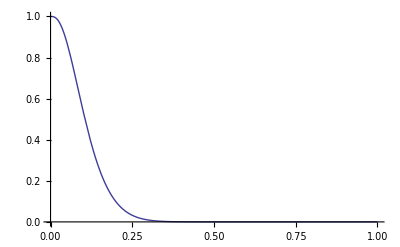

```mathematica
Plot[CDF[BinomialDistribution[25,p],2],{p,0,1},PlotRange->Full]
```

```mathematica
CDF[BinomialDistribution[25,0],2]
```

1

```mathematica
ExpectedValue[x^4,PoissonDistribution[μ],x]
```

μ+7 μ^2+6 μ^3+μ^4

```mathematica
Skewness[UniformDistribution[{α,β}]]
```

0

```mathematica
Kurtosis[UniformDistribution[{α,β}]]
```

9/5

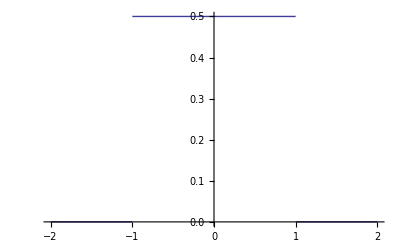

```mathematica
Plot[PDF[UniformDistribution[{-1,1}],x],{x,-2,2}]
```

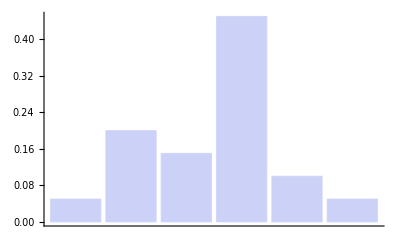

```mathematica
BarChart[{0.05,0.20,0.15,0.45,0.10,0.05}]
```

```mathematica
Integrate[(β/π x^2)/((x-α)^2+β^2),x]
```

(β (x+((α^2-β^2) ArcTan[(x-α)/β])/β+α Log[x^2-2 x α+α^2+β^2]))/π

```mathematica
Series[(1-β t)^(-α),{t,0,5}]
```

1+α β t+1/2 α (1+α) β^2 t^2+1/6 α (1+α) (2+α) β^3 t^3+1/24 α (1+α) (2+α) (3+α) β^4 t^4+1/120 α (1+α) (2+α) (3+α) (4+α) β^5 t^5+O[t]^6

```mathematica
D[x^((v-2)/2)ⅇ^(-x/2),x]//Simplify
```

-1/2 ⅇ^(-x/2) x^(-2+v/2) (2-v+x)

```mathematica
Integrate[k x^(β-1) ⅇ^(-α x^β),{x,0,∞}]
```

2 α If[Re[α]>0,(√π)/(4 α^(3/2)),Integrate[ⅇ^(-x^2 α) x^2,{x,0,∞},Assumptions→Re[α]≤0]]

```mathematica
Integrate[k x^(β-1) ⅇ^(-α x^β),x]
```

-(ⅇ^(-x^β α) k)/(α β)

```mathematica
Integrate[x^1 (1-x)^2,{x,0,1}]
```

1/12

```mathematica
D[x^(α-1)(1-x)^(β-1),x]//Simplify
```

(1-x)^(-2+β) x^(-2+α) (-1+α-x (-2+α+β))

```mathematica
Apart[(x-d)/(-b x^2+b x),x]//TraditionalForm
```

(d-1)/(b (x-1))-d/(b x)

```mathematica
Integrate[(d-1)/(b (x-1))-d/(b x),x]
```

((-1+d) Log[-1+x]-d Log[x])/b

```mathematica
CDF[NormalDistribution[18.7,9.1],10.6]
```

0.186703

```mathematica
D[1/(σ √(2π))ⅇ^(-1/2((x-μ)/σ)^2),{x,2}]//Simplify
```

(ⅇ^(-(x-μ)^2/(2 σ^2)) (x^2-2 x μ+μ^2-σ^2))/(√(2 π) σ^5)

```mathematica
Skewness[NormalDistribution[μ,σ]]
```

0

```mathematica
Kurtosis[NormalDistribution[μ,σ]]
```

3

```mathematica
D[ⅇ^(μ t+1/2 σ^2 t^2-c t),{t,3}]//Simplify
```

ⅇ^(1/2 t (-2 c+2 μ+t σ^2)) (-c+μ+t σ^2) (3 σ^2+(-c+μ+t σ^2)^2)

```mathematica
D[ⅇ^(μ t+1/2 σ^2 t^2),{t,3}]//Simplify
```

ⅇ^(t μ+(t^2 σ^2)/2) (μ+t σ^2) (3 σ^2+(μ+t σ^2)^2)

```mathematica
(36Binomial[8,5])/Binomial[52,5]//N
```

0.000775695

```mathematica
Series[ⅇ^(1/2 t^2),{t,0,10}]
```

1+t^2/2+t^4/8+t^6/48+t^8/384+t^10/3840+O[t]^11

```mathematica
D[Log[f[x]],{x,4}]
```

-(6 f'[x]^4)/f[x]^4+(12 f'[x]^2 f''[x])/f[x]^3-(3 f''[x]^2)/f[x]^2-(4 f'[x] f^(3)[x])/f[x]^2+(f^(4)[x])/f[x]

```mathematica
Integrate[μ^2 ⅇ^(-1/2 μ^2),{μ,0,∞}]
```

√(π/2)

```mathematica
Collect[((x-Subscript[μ, 1])/Subscript[σ, 1])^2-2ρ((x-Subscript[μ, 1])/Subscript[σ, 1])((a x+b-Subscript[μ, 2])/Subscript[σ, 2])+((a x+b-Subscript[μ, 2])/Subscript[σ, 2])^2,x]
```

μ_1^2/σ_1^2+x^2 (1/σ_1^2+a^2/σ_2^2-(2 a ρ)/(σ_1 σ_2))+x (-(2 μ_1)/σ_1^2+(2 a b)/σ_2^2-(2 a μ_2)/σ_2^2-(2 b ρ)/(σ_1 σ_2)+(2 a ρ μ_1)/(σ_1 σ_2)+(2 ρ μ_2)/(σ_1 σ_2))+b^2/σ_2^2-(2 b μ_2)/σ_2^2+μ_2^2/σ_2^2+(2 b ρ μ_1)/(σ_1 σ_2)-(2 ρ μ_1 μ_2)/(σ_1 σ_2)

```mathematica
D[ⅇ^(Subscript[t, 1] Subscript[μ, 1]+Subscript[t, 2] Subscript[μ, 2]+1/2(Subscript[σ, 1]^2 Subscript[t, 1]^2+2ρ Subscript[σ, 1] Subscript[σ, 2] Subscript[t, 1] Subscript[t, 2]+Subscript[σ, 2]^2 Subscript[t, 2]^2)),Subscript[t, 1],Subscript[t, 2]]
```

ⅇ^(t_1 μ_1+t_2 μ_2+1/2 (t_1^2 σ_1^2+2 ρ t_1 t_2 σ_1 σ_2+t_2^2 σ_2^2)) ρ σ_1 σ_2+ⅇ^(t_1 μ_1+t_2 μ_2+1/2 (t_1^2 σ_1^2+2 ρ t_1 t_2 σ_1 σ_2+t_2^2 σ_2^2)) (μ_1+1/2 (2 t_1 σ_1^2+2 ρ t_2 σ_1 σ_2)) (μ_2+1/2 (2 ρ t_1 σ_1 σ_2+2 t_2 σ_2^2))

```mathematica
CDF[GammaDistribution[3,2],12]//N
```

0.938031

```mathematica
Integrate[1/16 x^2 ⅇ^(-1/2 x),{x,0,12}]//N
```

0.938031

```mathematica
(f+g)^6
```

```mathematica
1-CDF[NormalDistribution[μ,σ],4σ+μ]//N
```

0.0000316712

```mathematica
Solve[CDF[NormalDistribution[0,1],z]==0.5,z]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→0.}}

```mathematica
PDF[BinomialDistribution[150,1/20],1]//N
```

0.00359649

```mathematica
√(10000*0.5*0.5)
```

50.

```mathematica
CDF[NormalDistribution[5000,50],5100.5]-CDF[NormalDistribution[5000,50],4899.5]
```

0.955569

```mathematica
PDF[PoissonDistribution[7.5],1]
```

0.00414813

```mathematica
ContourPlot3D[{x==y+z,y==0,z==0},{x,0,1},{y,0,1},{z,0,1},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
PDF[HypergeometricDistribution[2,3,6],2]//N
```

0.2

```mathematica
Apart[1/(π^2(1+x^2)(1+(y-x)^2)),x]
```

(2 x+y)/(π^2 (1+x^2) y (4+y^2))+(-2 x+3 y)/(π^2 y (4+y^2) (1+x^2-2 x y+y^2))

```mathematica
Integrate[1/(π^2(1+x^2)(1+(y-x)^2)),x]
```

(y ArcTan[x]+y ArcTan[x-y]+Log[1+x^2]-Log[1+(x-y)^2])/(π^2 y (4+y^2))

```mathematica
Integrate[1/(π^2(1+((Subscript[y, 1]+Subscript[y, 2])/2)^2)(1+((Subscript[y, 1]-Subscript[y, 2])/2)^2))1/2,Subscript[y, 2]]
```

-(Log[4+y_1^2-2 y_1 y_2+y_2^2]-Log[4+(y_1+y_2)^2]+(ArcTan[2/(-y_1+y_2)]+ArcTan[2/(y_1+y_2)]) y_1)/(π^2 y_1 (4+y_1^2))

```mathematica
Apart[1/(π^2(1+((Subscript[y, 1]+Subscript[y, 2])/2)^2)(1+((Subscript[y, 1]-Subscript[y, 2])/2)^2))1/2,Subscript[y, 2]]
```

(2 (2 y_1-y_2))/(π^2 y_1 (4+y_1^2) (4+y_1^2-2 y_1 y_2+y_2^2))+(2 (2 y_1+y_2))/(π^2 y_1 (4+y_1^2) (4+y_1^2+2 y_1 y_2+y_2^2))

```mathematica
ContourPlot3D[{u==y,u==y+1,y==z,y==z+1,z==0,z==1},{u,0,5},{y,0,5},{z,0,5},AxesLabel->{u,y,z}]
```

-Graphics3D-

```mathematica
D[(θ^k ⅇ^(k t))/((1-ⅇ^t(1-θ))^k),{t,2}]/.t -> 0//Simplify
```

(k (1+k-θ))/θ^2

```mathematica
RandomReal[NormalDistribution[0,1],10]
```

{-0.098825,-0.522243,-1.25018,0.790289,-1.11021,-1.1961,-1.06813,1.16605,0.464181,1.79173}

```mathematica
CDF[ChiSquareDistribution[15],(15*54.668)/25]-CDF[ChiSquareDistribution[15],(15*12.102)/25]
```

0.944991

Sec1.6

```mathematica
(Binomial[100,5]Binomial[95,5])/2
```

2181098991511440

1.21

```mathematica
Multinomial[4,3]
```

35

1.22

```mathematica
(4!3!)/(2!2!2!)
```

18

1.23

```mathematica
3!2^3
```

48

1.27

```mathematica
Multinomial[3,4,5]
```

27720

1.28

```mathematica
4^8
Multinomial[2,2,2,2]
```

65536

2520

1.29

```mathematica
Multinomial[3,4,2,1]
3*3Multinomial[4,2,1]
```

12600

945

1.30

```mathematica
7!*2*8*7
```

564480

1.6

```mathematica
7^4
```

2401

1.14

```mathematica
Binomial[52,5]
```

2598960

1.17

```mathematica
(10!)/(3!)
```

604800

1.32

```mathematica
Binomial[13,5]
Binomial[10,5]Binomial[8,5]
```

1287

14112

1.33

```mathematica
Binomial[12,3]
Binomial[12,3]+Binomial[13,2]+Binomial[13,2]
+Binomial[14,2]+Binomial[15,2]
```

220

572

self1.17

```mathematica
(k(k-1))/(2!)+((n-k)(n-k-1))/(2!)+k(n-k)
```

self1.4

```mathematica
(Binomial[8,2]Binomial[2,1]+Binomial[8,3])3!
```

672

theo1.13

```mathematica
n(n-1)(n-2)+2*3n(n-1)+2^2 n//Simplify
```

n^2 (3+n)

exa5h

```mathematica
3/4 2/4 1/4//N
```

0.09375

```mathematica
39/51 26/50 13/49//N
```

0.105498

```mathematica
(4!Multinomial[12,12,12,12])/Multinomial[13,13,13,13]//N
```

0.105498

exa5j

```mathematica
Permutations[{Ah,As,2c,3d}]
```

```mathematica
{{Ah,As,2 c,3 d},{Ah,As,3 d,2 c},{Ah,2 c,As,3 d},{Ah,2 c,3 d,As},{Ah,3 d,As,2 c},{Ah,3 d,2 c,As},{As,Ah,2 c,3 d},{As,Ah,3 d,2 c},{As,2 c,Ah,3 d},{As,2 c,3 d,Ah},{As,3 d,Ah,2 c},{As,3 d,2 c,Ah},{2 c,Ah,As,3 d},{2 c,Ah,3 d,As},{2 c,As,Ah,3 d},{2 c,As,3 d,Ah},{2 c,3 d,Ah,As},{2 c,3 d,As,Ah},{3 d,Ah,As,2 c},{3 d,Ah,2 c,As},{3 d,As,Ah,2 c},{3 d,As,2 c,Ah},{3 d,2 c,Ah,As},{3 d,2 c,As,Ah}}
```

```mathematica
{{Ah,As,2 c,3 d},{Ah,As,3 d,2 c},{Ah,2 c,As,3 d},{Ah,2 c,3 d,As},{Ah,3 d,As,2 c},{Ah,3 d,2 c,As},{As,Ah,2 c,3 d},{As,Ah,3 d,2 c},{As,2 c,Ah,3 d},{As,2 c,3 d,Ah},{As,3 d,Ah,2 c},{As,3 d,2 c,Ah},{2 c,Ah,As,3 d},{2 c,Ah,3 d,As},{2 c,As,Ah,3 d},{2 c,As,3 d,Ah},{2 c,3 d,Ah,As},{2 c,3 d,As,Ah},{3 d,Ah,As,2 c},{3 d,Ah,2 c,As},{3 d,As,Ah,2 c},{3 d,As,2 c,Ah},{3 d,2 c,Ah,As},{3 d,2 c,As,Ah}}
```

2.15

```mathematica
(Binomial[13,3]Binomial[3,2]Binomial[4,2]Binomial[4,2]Binomial[4,1])/Binomial[52,5]//N
```

0.047539

```mathematica
(Binomial[13,2]Binomial[2,1]Binomial[4,1])/Binomial[52,5]//N
```

0.000240096

2-16

#### d

```mathematica
(Binomial[5,3]*6*5*4)/6^5//N
```

0.154321

#### b

```mathematica
(Binomial[5,2]*6*5*4*3)/6^5//N
```

0.462963

#### c

```mathematica
(Binomial[5,2]Binomial[3,2] 1/2*6*5*4)/6^5//N
```

0.231481

2-35

```mathematica
(Binomial[12,3]Binomial[34,4]+Binomial[16,3]Binomial[30,4]-Binomial[12,3]Binomial[16,3]Binomial[18,1])/Binomial[46,7]//N
```

0.43591

## 2-33

```mathematica
(Binomial[5,2]Binomial[15,2])/Binomial[20,4]
```

70/323

2-42

```mathematica
Table[1-(5/6)^i,{i,10}]//N
```

{0.166667,0.305556,0.421296,0.517747,0.598122,0.665102,0.720918,0.767432,0.806193,0.838494}

2-44

```mathematica
(2*3*3!)/(5!)
```

3/10

```mathematica
(2*3*2*2)/(5!)
```

1/5

```mathematica
(2*3!)/(5!)
```

1/10

2-49

```mathematica
(Multinomial[3,3]Multinomial[3,3])/Multinomial[6,6]//N
```

0.4329

2-50

```mathematica
(Binomial[13,5]Binomial[39,8]Binomial[8,8]Binomial[31,5]Multinomial[13,13])/Multinomial[13,13,13,13]//N
```

2.6084×10^-6

```mathematica
Binomial[13,5](13!47!)/(52!8!)(13!39!)/(47!5!)//N
```

2.6084×10^-6

2-26

```mathematica
8/36+2(3/36)^2/(1-27/36)+2(4/36)^2/(1-26/36)+2(5/36)^2/(1-25/36)//N
```

0.492929

2-28

```mathematica
(3!*5*6*8)/19^3//N
```

0.209943

2-30

```mathematica
4/8*4/9*1/4
```

1/18

```mathematica
4/8+4/9-2 4/8*4/9
```

1/2

2-47

```mathematica
(12!)/12^12//N
```

0.0000537232

2-20

```mathematica
1-(2(Binomial[4,1]Binomial[16,1])/Binomial[52,2]-(Binomial[4,1]Binomial[3,1]Binomial[16,1]Binomial[15,1])/(Binomial[52,2]Binomial[50,2]))//N
```

0.905242

2-34

```mathematica
Binomial[32,13]/Binomial[52,13]//N
```

0.000547033

2-37

```mathematica
Binomial[7,5]/Binomial[10,5]//N
```

0.0833333

```mathematica
Binomial[7,5]/Binomial[10,5]+(Binomial[7,4]Binomial[3,1])/Binomial[10,5]//N
```

0.5

2-54

```mathematica
(Binomial[4,1]Binomial[39,13])/Binomial[52,13]-(Binomial[4,2]Binomial[26,13])/Binomial[52,13]+(Binomial[4,3]Binomial[13,13])/Binomial[52,13]//N
```

0.0510655

2-52

```mathematica
(Binomial[10,8] 2^8)/Binomial[20,8]//N
```

0.0914503

```mathematica
(Binomial[10,1]Binomial[9,6] 2^6)/Binomial[20,8]//N
```

0.426768

self2.12

```mathematica
(Binomial[6,2]Binomial[4,2]2Multinomial[2,2] 1/2)/(Multinomial[2,2,2,2,2]/(5!))//N
```

0.571429

self2.11

```mathematica
(4Binomial[13,2] 13^3)/Binomial[52,5]//N
```

0.263745

3-13

```mathematica
(Multinomial[12,12,12,12]Multinomial[1,1,1,1])/Multinomial[13,13,13,13]//N
```

0.105498

3-3

```mathematica
((Binomial[13,8]Binomial[39,18]Binomial[5,3]Binomial[21,10])/(Binomial[52,26]Binomial[26,13]))/((Binomial[13,8]Binomial[39,18])/Binomial[52,26])//N
```

0.33913

3-9

```mathematica
(1/3 2/3 3/4+1/3 1/3 1/4)/(1/3 2/3 3/4+1/3 1/3 1/4+2/3 2/3 1/4)
```

7/11

3-15

```mathematica
(0.32*2)/(0.32*2+0.68)
```

0.484848

3-11

```mathematica
(4*3)/(2*4*48+4*3)
```

1/33

3-17

```mathematica
0.36*0.22
```

0.0792

```mathematica
(0.36*0.22)/0.3
```

0.264

3-19

```mathematica
(0.38*0.48)/(0.38*0.48+0.62*0.37)
```

0.442933

```mathematica
0.38*0.48+0.62*0.37
```

0.4118

3-28

```mathematica
48*32
```

1536

3-40

```mathematica
(7*8*9)/(12*13*14)
```

3/13

```mathematica
(5*7*8)/(12*13*14)*3
```

5/13

```mathematica
(5*6*7)/(12*13*14)
```

5/52

3-41

```mathematica
3(26/51 1/27)+1/27
```

43/459

3-49

```mathematica
(0.70*0.268)/(0.70*0.268+0.30*0.135)
```

0.822446

3-50

```mathematica
0.20*0.05+0.5*0.15+0.3*0.3
```

0.175

```mathematica
(0.20*0.05)/(0.20*0.05+0.5*0.15+0.3*0.3)//N
```

0.0571429

3-52

```mathematica
0.6*0.15+0.4*0.05
```

0.11

```mathematica
(0.6*0.20+0.4*0.10)/(0.6*0.85+0.4*0.95)
16/89//N
```

0.179775

0.179775

```mathematica
(0.6*0.4)/(0.6*0.4+0.4*0.75)
12/27//N
```

0.444444

0.444444

```mathematica
(0.6*0.15)/(0.6*0.15+0.4*0.4)
9/25//N
```

0.36

0.36

exa4i

```mathematica
1/(1+((0.6(1-0.4))/(0.4(1-0.6)))^10)
```

0.000300638

3-81

```mathematica
(1-(9/11)^15)/(1-(9/11)^30)//N
```

0.953027

3-82

```mathematica
Solve[x==(1-Subscript[p, 1])(1-x)+Subscript[p, 1](1-Subscript[p, 1])(1-x)+Subscript[p, 1]^2,x]
```

{{x→-1/(-2+p_1^2)}}

3-89

```mathematica
(0.7*0.7*0.7)/(0.7*0.7*0.7+0.3*0.2*0.2)*0.7+(0.3*0.2*0.2)/(0.7*0.7*0.7+0.3*0.2*0.2)*0.2
97/142//N
```

0.683099

0.683099

```mathematica
(0.7*0.7*0.3)/(0.7*0.7*0.3+0.3*0.2*0.8)*0.7+(0.3*0.2*0.8)/(0.7*0.7*0.3+0.3*0.2*0.8)*0.2
15/26//N
```

0.576923

0.576923

Sec4.7

```mathematica
ⅇ^-1//N
```

0.367879

4-22

```mathematica
D[2 p^2+2(1-p)^2+3 p^2(1-p)*3+3p(1-p)^2*3,p]//Simplify
Solve[D[2 p^2+2(1-p)^2+3 p^2(1-p)*3+3p(1-p)^2*3,p]==0,p]
```

5-10 p

{{p→1/2}}

```mathematica
D[2 p^2+2(1-p)^2,p]//Simplify
```

-4+8 p

4-31

```mathematica
(1-(1-p)^2)x+(1-p^2)(1-x)//Simplify
D[(1-(1-p)^2)x+(1-p^2)(1-x),p]//Simplify
Solve[D[(1-(1-p)^2)x+(1-p^2)(1-x),p]==0,p]
```

1-p^2-x+2 p x

-2 p+2 x

{{p→x}}

4-26

```mathematica
1*1/10+2*9/10 1/5+3*9/10 4/5 1/2+4*9/10 4/5 1/2
```

149/50

4-32

```mathematica
1*(0.9)^10+11*(1-(0.9)^10)
```

7.51322

4-40

```mathematica
1-CDF[BinomialDistribution[5,1/3],3]//N
11/243//N
```

0.0452675

0.0452675

4-43

```mathematica
1-CDF[BinomialDistribution[5,0.2],2]//N
```

0.05792

4-47

```mathematica
a={CDF[BinomialDistribution[9,0.3],4],CDF[BinomialDistribution[8,0.3],4],CDF[BinomialDistribution[7,0.3],3]}
```

{0.901191,0.942032,0.873964}

```mathematica
b={CDF[BinomialDistribution[9,0.7],4],CDF[BinomialDistribution[8,0.7],4],CDF[BinomialDistribution[7,0.7],3]}
```

{0.0988087,0.194104,0.126036}

```mathematica
0.6a+0.4b
```

{0.580238,0.642861,0.574793}

4-50

```mathematica
Binomial[7,5]/Binomial[10,6]
```

1/10

4-53

```mathematica
CDF[PoissonDistribution[80000*(1/365)^2],0]//N
80000*(1/365)^2//N
```

0.548544

0.600488

4-60

```mathematica
(3/4 PDF[PoissonDistribution[3],2])/(1/4 PDF[PoissonDistribution[5],2]+3/4 PDF[PoissonDistribution[3],2])//N
```

0.888644

4-63

```mathematica
ⅇ^-2.5//N
```

0.082085

4-64

```mathematica
1-CDF[PoissonDistribution[4],7]//N
```

0.0511336

4-65

```mathematica
1-CDF[PoissonDistribution[1/2],0]//N
```

0.393469

```mathematica
(1-CDF[PoissonDistribution[1/2],1])/(1-CDF[PoissonDistribution[1/2],0])//N
```

0.229253

```mathematica
1-CDF[PoissonDistribution[1/2],0]//N
```

0.393469

4-69

```mathematica
ⅇ^(-10/2^(4+1+1))-ⅇ^(-10/2^(4+1))//N
```

0.12373

4-80

```mathematica
Binomial[20,2]/Binomial[80,2]//N
```

0.0601266

theo4-23

```mathematica
1-CDF[BinomialDistribution[88,1/365],2]//N
```

0.00189663

```mathematica
PDF[PoissonDistribution[365(1-CDF[BinomialDistribution[88,1/365],2])],0]//N
```

0.500438

5-18

```mathematica
(4/0.84)^2
```

22.6757

5-23

```mathematica
CDF[NormalDistribution[1000*1/6,√(1000*1/6*5/6)],200.5]-CDF[NormalDistribution[1000*1/6,√(1000*1/6*5/6)],149.5]//N
```

0.925345

```mathematica
CDF[NormalDistribution[800*1/5,√(800*1/5*4/5)],149.5]-CDF[NormalDistribution[800*1/5,√(800*1/5*4/5)],-0.5]//N
```

0.176684

```mathematica
(200.5-1000*1/6)/(√(1000*1/6*5/6))//N
(149.5-1000*1/6)/(√(1000*1/6*5/6))//N
```

2.87085

-1.45664

```mathematica
0.9979-(1-0.9279)
```

0.9258

```mathematica
(149.5-800*1/5)/(√(800*1/5*4/5))//N
(-0.5-800*1/5)/(√(800*1/5*4/5))//N
```

-0.928078

-14.1863

```mathematica
(1-0.7995)-(
```

```mathematica
CDF[BinomialDistribution[800,1/5],149]//N
```

0.176985

5-27

```mathematica
√(10000*1/2*1/2)
```

50

```mathematica
N[CDF[NormalDistribution[10000*1/2,√(1000*1/2*1/2)],5799.5],1000000]
```

1.

```mathematica
N[1-CDF[NormalDistribution[μ,σ],7σ+μ],100]
```

1.27981254388583500438362369078083299803284415419871792902220432522852623942938009297615403705551705×10^-12

```mathematica
Table[CDF[NormalDistribution[μ,σ],μ+i σ]-CDF[NormalDistribution[μ,σ],μ-i σ],{i,10}]//N
```

{0.682689,0.9545,0.9973,0.999937,0.999999,1.,1.,1.,1.,1.}

5-31

```mathematica
∫(x-a)λ ⅇ^(-λ x)ⅆx
```

(ⅇ^(-x λ) (-1+a λ-x λ))/λ

```mathematica
-(ⅇ^(-x λ) (-1+a λ-x λ))/λ/.x->a
```

ⅇ^(-a λ)/λ

```mathematica
∫(a-x)λ ⅇ^(-λ x)ⅆx
```

(ⅇ^(-x λ) (1-a λ+x λ))/λ

```mathematica
((ⅇ^(-x λ) (1-a λ+x λ))/λ/.x->a)-((ⅇ^(-x λ) (1-a λ+x λ))/λ/.x->0)
```

ⅇ^(-a λ)/λ-(1-a λ)/λ

```mathematica
D[ⅇ^(-a λ)/λ+ⅇ^(-a λ)/λ-(1-a λ)/λ,a]
```

1-2 ⅇ^(-a λ)

5-35

```mathematica
ⅇ^(-∫_40^50 (0.027+0.00025(t-40)^2)ⅆt)
```

0.702343

Theo5-10

```mathematica
D[PDF[NormalDistribution[μ,σ],x],{x,2}]
```

((ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ)^2)/σ^4-(ⅇ^(-(x-μ)^2/(2 σ^2)))/σ^2)/(√(2 π) σ)

Theo5-11

```mathematica
PDF[NormalDistribution[0,1],x]
D[PDF[NormalDistribution[0,1],x],{x,1}]
```

(ⅇ^(-x^2/2))/(√(2 π))

-(ⅇ^(-x^2/2) x)/(√(2 π))

Theo5-28

```mathematica
D[PDF[BetaDistribution[a,b],x],{x,1}]
```

((-1+a) (1-x)^(-1+b) x^(-2+a))/Beta[a,b]-((-1+b) (1-x)^(-2+b) x^(-1+a))/Beta[a,b]

```mathematica
Solve
```

Theo5-24

```mathematica
ⅇ^-1//N
```

0.367879

Self5-14

```mathematica
∫2 x^2 ⅇ^(-x^2)ⅆx
```

2 (-1/2 ⅇ^(-x^2) x+1/4 √π Erf[x])

```mathematica
Limit[2 (-1/2 ⅇ^(-x^2) x+1/4 √π Erf[x]),x->Infinity]
```

(√π)/2

```mathematica
2 (-1/2 ⅇ^(-x^2) x+1/4 √π Erf[x])/.x->0
```

0

Self5-17

```mathematica
1000/36//N
10000/36//N
```

27.7778

277.778

```mathematica
1-CDF[NormalDistribution[10000*1/38,√(10000*1/38*37/38)],10000/36]//N
```

0.180535

6-12

```mathematica
CDF[PoissonDistribution[1/2*10],3]//N
39.3 ⅇ^-5//N
∑_(i=0)^3 5^i/(i!)//N
```

0.265026

0.264801

39.3333

6-26

```mathematica
Integrate[1,{x,0,1/4},{y,0,1},{z,√(4x y),1}]+Integrate[1,{x,1/4,1},{y,0,1/(4x)},{z,√(4x y),1}]
```

5/36+Log[2]/6

6-28

```mathematica
∫_0^2 x ⅇ^-x ⅆx
```

1-3/ⅇ^2

6-30

```mathematica
Integrate[1/(√(2π)25)ⅇ^(-(x+10)^2/(2*25^2)),{x,0.5,∞}]
```

0.337243

```mathematica
(0.5+10)/25
10/25//N
```

0.42

0.4

```mathematica
Integrate[1/(√(2π)25)ⅇ^(-(x-330)^2/(2*25^2)),{x,350.5,∞}]//N
```

0.206108

6-45

```mathematica
∑_(i=3)^5 Binomial[5,i](∫_0^y x ⅇ^-x ⅆx)^i(1-∫_0^y x ⅇ^-x ⅆx)^(5-i)
```

10 ⅇ^(-2 y) (1+y)^2 (1-ⅇ^-y (1+y))^3+5 ⅇ^-y (1+y) (1-ⅇ^-y (1+y))^4+(1-ⅇ^-y (1+y))^5

```mathematica
D[∑_(i=3)^5 Binomial[5,i](∫_0^y x ⅇ^-x ⅆx)^i(1-∫_0^y x ⅇ^-x ⅆx)^(5-i),y]//Simplify
```

30 ⅇ^(-5 y) y (1+y)^2 (1-ⅇ^y+y)^2

```mathematica
Multinomial[2,1,2](∫_0^y x ⅇ^-x ⅆx)^2(1-∫_0^y x ⅇ^-x ⅆx)^2 y ⅇ^-y//Simplify
```

30 ⅇ^(-5 y) y (1+y)^2 (1-ⅇ^y+y)^2

7-2

```mathematica
(6-S)(6-w)(9-R)//Expand
```

324-36 R-54 S+6 R S-54 w+6 R w+9 S w-R S w

```mathematica
324-36 *8/18*3-54 *5/18*3+6 *Binomial[16,1]/Binomial[18,3]*40-54*5/18*3+6 Binomial[16,1]/Binomial[18,3]*40+9 Binomial[16,1]/Binomial[18,3]*25-1/Binomial[18,3]*200//N
```

199.578

7-1

```mathematica
52.5/12//N
```

4.375

7-12

```mathematica
2/(2n)n/(2n-1)+(2n-2)/(2n)(1-Binomial[n-1,2]/Binomial[2n-1,2])//Simplify
```

(1-3 n)/(2-4 n)

```mathematica
(1-Binomial[n-1,2]/Binomial[2n-1,2])//Simplify
```

(3 n)/(-2+4 n)

7-21

```mathematica
365PDF[BinomialDistribution[100,1/365],3]//N
```

0.930145

```mathematica
365(1-(364/365)^100)//N
```

87.5755

7-22

```mathematica
∑_(i=1)^6 Binomial[6,i]*1/(i/6)*(-1)^(i+1)//N
```

14.7

```mathematica
∑_(i=0)^5 1/((6-i)/6)//N
```

14.7

7-23

```mathematica
5(1-10/11 9/10)(1-19/20 18/19 17/18)+8(1-19/20 18/19 17/18)
```

147/110

7-29

```mathematica
2*1/(1/8)+2*1/(3/8)-1/(2/8)-4 1/(4/8)-1/(6/8)+2 1/(7/8)+2 1/(5/8)-1
```

437/35

```mathematica
2*1/(1/8)-1/(2/8)
```

12

```mathematica
2*1/(3/8)-1/(6/8)
```

4

```mathematica
12+4-437/35
```

123/35

7-34

```mathematica
10(2/19-(2/19)^2)+2Binomial[10,2](20/Binomial[20,2] 1/(18*17)+20/Binomial[20,2] 3/(18*17)+(Binomial[20,2]-40)/Binomial[20,2](2*2)/(18*17)-(2/19)^2)
```

360/361

```mathematica
2Binomial[10,2](20/Binomial[20,2] 1/(18*17)+20/Binomial[20,2] 3/(18*17)+(Binomial[20,2]-40)/Binomial[20,2](2*2)/(18*17))+10*2/19-(10*2/19)^2
```

360/361

7-35

```mathematica
48*2/(4+1)+2//N
```

21.2

```mathematica
39*5/(13+1)+5//N
```

18.9286

```mathematica
39*13/(13+1)+13//N
```

49.2143

7-38

```mathematica
∫_0^∞ 2x ⅇ^(-2x)ⅆx
```

1/2

```mathematica
∫_0^∞ x ⅇ^(-2x)ⅆx
```

1/4

```mathematica
∫_0^∞ x^2 ⅇ^(-2x)ⅆx
```

1/4

7-40

```mathematica
∫_0^∞ y ⅇ^-y ⅆy
```

1

```mathematica
∫_0^∞ ∫_0^∞ x/y ⅇ^(-(y+x/y))ⅆxⅆy
```

1

```mathematica
∫_0^∞ y ⅇ^-y ⅆy
```

1

```mathematica
∫_0^∞ y^2 ⅇ^-y ⅆy
```

2

7-43

```mathematica
((((1+m+n)(m+n))/2)^2-((m+n)(m+n+1)(2(m+n)+1))/6)(n(n-1))/((m+n)(m+n+1))+(n(1+m+n))/2-((n(1+m+n))/2)^2//Simplify
```

1/12 n (-3 m^2+m (7-13 n)+2 (4+n-5 n^2))

7-60

```mathematica
Table[(2(m+2))/(m+1)(1-(1/2)^(m+1)),{m,30}]//N
```

{2.25,2.33333,2.34375,2.325,2.29688,2.26786,2.24121,2.21788,2.19785,2.18075,2.16614,2.15358,2.14273,2.13327,2.12497,2.11763,2.1111,2.10526,2.1,2.09524,2.09091,2.08696,2.08333,2.08,2.07692,2.07407,2.07143,2.06897,2.06667,2.06452}

7-63

```mathematica
x (12-x)/20 8//Expand
```

(24 x)/5-(2 x^2)/5

```mathematica
24/5 12/30*10-2/5*(10*9*12/30 11/29+12/30 10)-12/30 10*12/30 8
```

-96/145

7-65

```mathematica
3*0.4+5*0.6
```

4.2

```mathematica
(3+9)*0.4+(5+25)*0.6-(3*0.4+5*0.6)^2
```

5.16

7-66

```mathematica
Solve[x ==1/3(9+25+x+10*15+49+x+14*15),x]
```

{{x→443}}

```mathematica
443-15^2
```

218

7-67

```mathematica
((2p-1)+1)p+(1-(2p-1))(1-p)//Expand
```

2-4 p+4 p^2

7-73

```mathematica
1/(2π σ)∫_(-∞)^∞ ⅇ^(-(s-μ)^2/(2 σ^2)-(r-s)^2/2)ⅆs
```

1/(2 π σ)If[Re[1/σ^2]>-1&&(Re[r+μ/σ^2]<0||Re[σ^2]≠-1),(ⅇ^(-(r-μ)^2/(2 (1+σ^2))) √(2 π))/(√(1+1/σ^2)),Integrate[ⅇ^(-1/2 (r-s)^2-(s-μ)^2/(2 σ^2)),{s,-∞,∞},Assumptions→(Re[σ^2]==-1&&Re[r+μ/σ^2]≥0)||Re[1/σ^2]≤-1]]

7-74

```mathematica
∫_0^(1/2) x/(1/2) ⅆx
∫_(1/2)^1 x/(1/2) ⅆx
```

1/4

3/4

```mathematica
∫_0^(1/2) (x -1/4)^2 ⅆx+∫_(1/2)^1 (x -3/4)^2 ⅆx
```

1/48

7-77

```mathematica
∫_0^∞ ∫_(-∞)^∞ ⅇ^(t x+s y-y-(x-y)^2/2)ⅆxⅆy
```

√(2 π) If[Re[s+t]<1,-(ⅇ^(t^2/2))/(-1+s+t),Integrate[ⅇ^(t^2/2+(-1+s) y+t y),{y,0,∞},Assumptions→Re[s+t]≥1]]

7-79

```mathematica
Solve[CDF[NormalDistribution[40*2,√(6^2*2+0.6*6^2*2)],90]==1-z,z]//N
```

{{z→0.175747}}

```mathematica
Solve[CDF[NormalDistribution[40*2,√(6^2*2+0.2*6^2*2)],90]==1-z,z]//N
```

{{z→0.141002}}

T7-21

```mathematica
(i(i+1))/((n+1)(n+2))-i^2/(n+1)^2//Simplify
```

(i (1-i+n))/((1+n)^2 (2+n))

```mathematica
D[(i(i+1))/((n+1)(n+2))-i^2/(n+1)^2,i]//Simplify
```

(1-2 i+n)/((1+n)^2 (2+n))

```mathematica
Solve[D[(i(i+1))/((n+1)(n+2))-i^2/(n+1)^2,i]==0,i]
```

{{i→(1+n)/2}}

```mathematica
(i(i+1))/((n+1)(n+2))-i^2/(n+1)^2/.i->1//Simplify
```

n/((1+n)^2 (2+n))

```mathematica
(i(i+1))/((n+1)(n+2))-i^2/(n+1)^2/.i->n//Simplify
```

n/((1+n)^2 (2+n))

T7-23

```mathematica
D[ⅇ^(t^2/2),{t,3}]
```

3 ⅇ^(t^2/2) t+ⅇ^(t^2/2) t^3

```mathematica
D[ⅇ^(t^2/2),{t,2}]
```

ⅇ^(t^2/2)+ⅇ^(t^2/2) t^2

```mathematica
D[ⅇ^(t^2/2),{t,1}]
```

ⅇ^(t^2/2) t

7-38

```mathematica
(Y-(a+b*Subscript[X, 1]+c*Subscript[X, 2]))^2//Expand
```

a^2-2 a Y+Y^2+2 a b X_1-2 b Y X_1+b^2 X_1^2+2 a c X_2-2 c Y X_2+2 b c X_1 X_2+c^2 X_2^2

```mathematica
Solve[{2 a-2 Y+2 b Subscript[X, 1]+2 c Subscript[X, 2]==0,2 a Subscript[X, 1]-2 Y Subscript[X, 1]+2 b Subscript[X, 1]^2+2 c Subscript[X, 1] Subscript[X, 2]==0,2 a Subscript[X, 2]-2 Y Subscript[X, 2]+2 b Subscript[X, 1] Subscript[X, 2]+2 c Subscript[X, 2]^2==0},{a,b,c}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→Y-b X_1-c X_2}}

```mathematica
Solve[{2 a-2 f[Y]+2 b f[Subscript[X, 1]]+2 c f[ Subscript[X, 2]]==0,2 a f[Subscript[X, 1]]-2 f[Y Subscript[X, 1]]+2 b f[Subscript[X, 1]^2]+2 c f[Subscript[X, 1] Subscript[X, 2]]==0,2 a f[Subscript[X, 2]]-2 f[Y Subscript[X, 2]]+2 b f[Subscript[X, 1] Subscript[X, 2]]+2 c f[Subscript[X, 2]^2]==0},{a,b,c}]
```

{{a→-(-f[X_1^2] f[X_2] f[Y X_2]+f[Y X_1] f[X_2] f[X_1 X_2]+f[X_1] f[Y X_2] f[X_1 X_2]-f[Y] f[X_1 X_2]^2-f[X_1] f[Y X_1] f[X_2^2]+f[Y] f[X_1^2] f[X_2^2])/(f[X_1^2] f[X_2]^2-2 f[X_1] f[X_2] f[X_1 X_2]+f[X_1 X_2]^2+f[X_1]^2 f[X_2^2]-f[X_1^2] f[X_2^2]),b→-(-f[Y X_1] f[X_2]^2+f[X_1] f[X_2] f[Y X_2]+f[Y] f[X_2] f[X_1 X_2]-f[Y X_2] f[X_1 X_2]-f[Y] f[X_1] f[X_2^2]+f[Y X_1] f[X_2^2])/(f[X_1^2] f[X_2]^2-2 f[X_1] f[X_2] f[X_1 X_2]+f[X_1 X_2]^2+f[X_1]^2 f[X_2^2]-f[X_1^2] f[X_2^2]),c→-((-4 f[X_1]^2+4 f[X_1^2]) (4 f[Y] f[X_2]-4 f[Y X_2])-(4 f[Y] f[X_1]-4 f[Y X_1]) (-4 f[X_1] f[X_2]+4 f[X_1 X_2]))/(-(-4 f[X_1] f[X_2]+4 f[X_1 X_2])^2+(-4 f[X_1]^2+4 f[X_1^2]) (-4 f[X_2]^2+4 f[X_2^2]))}}

```mathematica
a^2-2 a f[Y]+f[Y^2]+2 a b f[Subscript[X, 1]]-2 b f[Y Subscript[X, 1]]+b^2 f[Subscript[X, 1]^2]+2 a c f[Subscript[X, 2]]-2 c f[Y Subscript[X, 2]]+2 b c f[Subscript[X, 1] Subscript[X, 2]]+c^2 f[Subscript[X, 2]^2]
```

```mathematica
D[a^2-2 a f[Y]+f[Y^2]+2 a b f[Subscript[X, 1]]-2 b f[Y Subscript[X, 1]]+b^2 f[Subscript[X, 1]^2]+2 a c f[Subscript[X, 2]]-2 c f[Y Subscript[X, 2]]+2 b c f[Subscript[X, 1] Subscript[X, 2]]+c^2 f[Subscript[X, 2]^2],a]
```

2 a-2 f[Y]+2 b f[X_1]+2 c f[X_2]

```mathematica
D[a^2-2 a f[Y]+f[Y^2]+2 a b f[Subscript[X, 1]]-2 b f[Y Subscript[X, 1]]+b^2 f[Subscript[X, 1]^2]+2 a c f[Subscript[X, 2]]-2 c f[Y Subscript[X, 2]]+2 b c f[Subscript[X, 1] Subscript[X, 2]]+c^2 f[Subscript[X, 2]^2],b]
```

2 a f[X_1]-2 f[Y X_1]+2 b f[X_1^2]+2 c f[X_1 X_2]

```mathematica
D[a^2-2 a f[Y]+f[Y^2]+2 a b f[Subscript[X, 1]]-2 b f[Y Subscript[X, 1]]+b^2 f[Subscript[X, 1]^2]+2 a c f[Subscript[X, 2]]-2 c f[Y Subscript[X, 2]]+2 b c f[Subscript[X, 1] Subscript[X, 2]]+c^2 f[Subscript[X, 2]^2],c]
```

2 a f[X_2]-2 f[Y X_2]+2 b f[X_1 X_2]+2 c f[X_2^2]

7-39

```mathematica
(Y-(a+b*Subscript[X, 1]+c*Subscript[X, 2]))^2//Expand
```

a^2-2 a Y+Y^2+2 a b X_1-2 b Y X_1+b^2 X_1^2+2 a c X_2-2 c Y X_2+2 b c X_1 X_2+c^2 X_2^2

```mathematica
D[a^2-2 a f[Y]+f[Y^2]+2 a b f[Subscript[X, 1]]-2 b f[Y Subscript[X, 1]]+b^2 f[Subscript[X, 1]^2]+2 a c f[Subscript[X, 2]]-2 c f[Y Subscript[X, 2]]+2 b c f[Subscript[X, 1] Subscript[X, 2]]+c^2 f[Subscript[X, 2]^2],a]
```

2 a-2 f[Y]+2 b f[X_1]+2 c f[X_2]

7-40

```mathematica
(1/p+1)^2(1-p)+p-(1/p)^2//Simplify
```

-1+1/p

T7-54

```mathematica
D[ⅇ^(t^2/2),{t,3}]
```

3 ⅇ^(t^2/2) t+ⅇ^(t^2/2) t^3

```mathematica
D[ⅇ^(t^2/2),{t,2}]
```

ⅇ^(t^2/2)+ⅇ^(t^2/2) t^2

```mathematica
D[ⅇ^(t^2/2),{t,1}]
```

ⅇ^(t^2/2) t

S7-11

```mathematica
10*3/19*12/20+10*1/19*8/20
```

22/19

```mathematica
10*3*3/95+10*4*1/190
```

22/19

8.5

```mathematica
D[(σ^2+b^2)/(a+b)^2,b]//Simplify
```

(2 (a b-σ^2))/(a+b)^3

8-4

```mathematica
1-CDF[NormalDistribution[20,√20],15.5]//N
```

0.842848

8-5

```mathematica
2(1-CDF[NormalDistribution[0,√(1/12*50)],3])//N
```

0.141645

8-9

```mathematica
Mean[GammaDistribution[n,1]]
```

n

```mathematica
Variance[GammaDistribution[n,1]]
```

n

```mathematica
ExpectedValue[x/n,GammaDistribution[n,1],x]
```

1

8-10

```mathematica
Solve[CDF[NormalDistribution[3n-400,√(0.3^2 n+40^2)],0]==0.9,n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→116.19}}

8-17

```mathematica
CDF[NormalDistribution[50.25,√25.126],30.5]//N
```

0.0000407266

8-23

```mathematica
20/26//N
```

0.769231

```mathematica
20/(20+6^2)//N
```

0.357143

```mathematica
Exp[20(26/20-1)](20/26)^26//N
```

0.439784

```mathematica
1-CDF[NormalDistribution[20,√20],25.5]//N
```

0.109379

T8-12

```mathematica
D[Exp[t a^2]((1/2)/(1/2-t))^(1/2),t]//Simplify
```

(ⅇ^(a^2 t) √(1/(1-2 t)) (-1+a^2 (-1+2 t)))/(-1+2 t)

```mathematica
Solve[(ⅇ^(a^2 t) √(1/(1-2 t)) (-1+a^2 (-1+2 t)))/(-1+2 t)==0,t]
```

{{t→(1+a^2)/(2 a^2)}}

```mathematica
Exp[t a^2]((1/2)/(1/2-t))^(1/2)/.t->(1+a^2)/(2 a^2)//Simplify
```

√(-a^2) ⅇ^(1/2 (1+a^2))

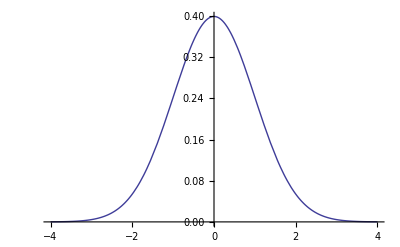

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]
```

```mathematica
PDF[NormalDistribution[0,1],0]
```

1/(√(2 π))

9-5

```mathematica
(({{0.7, 0.3}, {0.3, 0.7}})^3).({{0.5}, {0.5}})//MatrixForm
```

(0.185
0.185)

9-14

```mathematica
-Log[2,1/6]//N
-5/36 Log[2,1/6]-25/36 Log[2,5/6]//N
-5/36 Log[2,1/36]-25/36 Log[2,5/36]-1/6 Log[2,1/6]//N
```

2.58496

0.541685

3.12665

9-15

```mathematica
∑_(i=0)^6 -Binomial[6,i](2/3)^i(1/3)^(6-i)Log[2,(2/3)^i(1/3)^(6-i)]//N
```

5.50978

9-18

```mathematica
D[((1-a)p+a(1-p))Log[2,(1-a)p+a(1-p)]+((1-a)(1-p)+a p)Log[2,(1-a)(1-p)+a p],a]//Simplify
```

-((-1+2 p) (Log[a+p-2 a p]-Log[1-a-p+2 a p]))/Log[2]

Self9-3

```mathematica
NullSpace[({{1/5-1, 1/6}, {4/5, 5/6-1}})]
```

{{5/24,1}}

10-10

```mathematica
√(2/π)1/x ⅇ^(1/2 x^2)/.x->1/10//N
```

8.01884

```mathematica
D[√(2/π)1/x ⅇ^(1/2 x^2),x]
```

ⅇ^(x^2/2) √(2/π)-(ⅇ^(x^2/2) √(2/π))/x^2

10-11

```mathematica
D[x^3(1-x)^2,x]
```

3 (1-x)^2 x^2-2 (1-x) x^3

```mathematica
Solve[3 (1-x)^2 x^2-2 (1-x) x^3==0,x]
```

{{x→0},{x→0},{x→3/5},{x→1}}

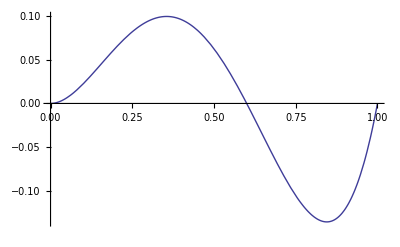

```mathematica
Plot[3 (1-x)^2 x^2-2 (1-x) x^3,{x,0,1}]
```

Expl

```mathematica
1-CDF[BinomialDistribution[10000,0.492929],10000/2-1]
```

0.08011387573

T1.5.8

```mathematica
(A∩B)^c=A^c∪B^c
```

Example 1.9.4

```mathematica
(Binomial[13,6]Binomial[13,4]Binomial[13,2]Binomial[13,1])/Binomial[52,13]//N
```

0.0019592

T1.10.2

```mathematica
Pr((∪^m)_(i=1)Subscript[A, i])
```

```mathematica
Pr(Subscript[A, m-2]∩Subscript[A, m-1]∩(Subscript[A, m]∪Subscript[A, m+1]))=Pr(Subscript[A, m-2]∩Subscript[A, m-1]∩Subscript[A, m])+Pr(Subscript[A, m-2]∩Subscript[A, m-1]∩Subscript[A, m+1])-Pr(Subscript[A, m-2]∩Subscript[A, m-1]∩Subscript[A, m]∩Subscript[A, m+1])
```

E2.1.5

```mathematica
6/36+(36-11)/36 6/36
```

```mathematica
(6/36)/(1-(36-11)/36)
```

6/11

The Game of Craps

```mathematica
(6+2)/36+Sum[i/36 i/(i+6),{i,{3,4,5,5,4,3}}]//N
```

0.492929

The Collector’s Problem

```mathematica
r=5;n=4r;∑_(j=0)^(r-1) (-1)^j Binomial[r,j](1-j/r)^n//N
```

0.942719

2.3.2

```mathematica
Pr(A|B)=(Pr(A∩B))/(Pr(B))
Pr(A|B∩C)=(Pr(A∩B|C))/(Pr(B|C))
```

```mathematica
(Pr(Subscript[B, 1]|Subscript[H, 1])Pr(Subscript[H, 2]|Subscript[B, 1]∩Subscript[H, 1]))/(Pr(Subscript[B, 1]|Subscript[H, 1])Pr(Subscript[H, 2]|Subscript[B, 1]∩Subscript[H, 1])+Pr(Subscript[B, 2]|Subscript[H, 1])Pr(Subscript[H, 2]|Subscript[B, 2]∩Subscript[H, 1]))=
```

```mathematica
(Pr(Subscript[H, 2]∩Subscript[B, 1]|Subscript[H, 1]))/(Pr(Subscript[H, 2]|Subscript[H, 1]))
```

2.4.4

```mathematica
Subscript[a, 1]=p Subscript[a, 2]+(1-p) Subscript[a, 0]
p Subscript[a, 1]+(1-p) Subscript[a, 1]=p Subscript[a, 2]+(1-p) Subscript[a, 0] 
p(Subscript[a, 2]-Subscript[a, 1])=(1-p) (Subscript[a, 1]-Subscript[a, 0])                
Subscript[a, 2]=p Subscript[a, 3]+(1-p) Subscript[a, 1]
(Subscript[a, 2]-Subscript[a, 1])=p (Subscript[a, 3]-Subscript[a, 2])+(1-p) (Subscript[a, 1]-Subscript[a, 0])
Subscript[a, 3]=p Subscript[a, 4]+(1-p) Subscript[a, 2]
(Subscript[a, 3]-Subscript[a, 2])=p (Subscript[a, 4]-Subscript[a, 3])+(1-p) (Subscript[a, 2]-Subscript[a, 1])
```

2.4.9

```mathematica
k=10000;p=0.45;i=9995;Subscript[a, i]=(((1-p)/p)^i-1)/(((1-p)/p)^k-1)//N
```

0.366648

Exercise 3.3.17

```mathematica
F^-1(SuperMinus[p])= L
|F^-1(y)- L|<ϵ
|y- p|<σ
```

Example 3.5.10

```mathematica
∫_(-√(1-x^2))^(+√(1-x^2)) k x^2 y^2 ⅆy
```

2/3 k x^2 (1-x^2)^(3/2)

```mathematica
k x^2 1/3 2(1-x^2)^(3/2)
```

```mathematica
∫_-1^1 k x^2 1/3 2(1-x^2)^(3/2)ⅆx=∫_(-π/2)^(π/2) 2/3 k Sin[θ]^2 Cos[θ]^4 ⅆθ=∫_(-π/2)^(π/2) 2/3 k Sin[θ]^2(1- Sin[θ]^2)^2 ⅆ θ
```

```mathematica
(1-Cos[2θ])/2((1+Cos[2θ])/2)^2=
```

```mathematica
Solve[∫_-1^1 k x^2 1/3 2(1-x^2)^(3/2)ⅆx==1,k]
```

{{k→24/π}}

Theorem 3.5.5

```mathematica
Subscript[f, 1](x)=Subscript[c, 1] Subscript[h, 1](x)
Subscript[f, 2](x)=1/Subscript[c, 1] Subscript[h, 2](x)
```

Example 3.7.15

```mathematica
∫_0^∞ 2 z^2 Exp[-z(2+Subscript[x, 1]+Subscript[x, 2])]ⅆz=[(2 z^2)/(-(2+Subscript[x, 1]+Subscript[x, 2]))Exp[-z(2+Subscript[x, 1]+Subscript[x, 2])]]-∫_0^∞ (4z)/(-(2+Subscript[x, 1]+Subscript[x, 2]))Exp[-z(2+Subscript[x, 1]+Subscript[x, 2])]ⅆz
=∫_0^∞ (4z)/(2+Subscript[x, 1]+Subscript[x, 2])Exp[-z(2+Subscript[x, 1]+Subscript[x, 2])]ⅆz=[(4z)/(-(2+Subscript[x, 1]+Subscript[x, 2])^2)Exp[-z(2+Subscript[x, 1]+Subscript[x, 2])]]-∫_0^∞ 4/(-(2+Subscript[x, 1]+Subscript[x, 2])^2)Exp[-z(2+Subscript[x, 1]+Subscript[x, 2])]ⅆz=∫_0^∞ 4/(2+Subscript[x, 1]+Subscript[x, 2])^2 Exp[-z(2+Subscript[x, 1]+Subscript[x, 2])]ⅆz
```

Theorem3.8.2

```mathematica
G(y)=Pr(Y≤y)=Pr(a X + b≤y)=Pr(X≤(y-b)/a)=∫_(-∞)^((y-b)/a) f(x)ⅆx    a>0
```

```mathematica
Pr(X>=(y-b)/a)=∫_((y-b)/a)^∞ f(x)ⅆx    a<0
```

E3.8-12

```mathematica
Pr(Y≤y)=Pr(F^-1(X)≤y)=Pr(X≤F(y))=F(y)
F(F^-1(X))≥X
F^-1(X)≤y⇔X≤F(y)
F^-1(0.7)≤ 10⇔0.7≤F(10)
```

E3.8-15

```mathematica
Pr(Y≤y)=Pr(X^2≤y)=Pr(-y^(1/2)≤X≤y^(1/2))=F( y^(1/2))- F( -y^(1/2))    y≥0
```

```mathematica
(F( y^(1/2))- F( -y^(1/2)) )'=f( y^(1/2))1/2 1/y^(1/2)-f( -y^(1/2)) (-1/2 1/y^(1/2))
```

Theorem3.10.4

Example4.1.11

```mathematica
F(y)=Pr(Y≤y)=Pr(r(X)≤y)=Pr(1/X≤y)=Pr(X≥1/y)=1-F(1/y)
```

```mathematica
-f(1/y)(-1/y^2)
```

Theorem 4.1.1

```mathematica
∫_(-∞)^(+∞) y f(y)ⅆy=∫_□^□ r(x) f(r(x))r'(x)ⅆx
```

```mathematica
∫_(-∞)^(+∞) z f(z)ⅆz
```

Exercises4.1-1

```mathematica
1/(b-a)x
```

Example
4.2.2

```mathematica
(b-a)*3%+a
```

Supplementary Exercises4.9-1

```mathematica
lim_(x->+∞) (x(1-∫_(-∞)^x f(t)ⅆt))=lim_(x->+∞) (x∫_x^∞ f(t)ⅆt)<=lim_(x->+∞) (∫_x^∞ t f(t)ⅆt)
```

```mathematica
lim_(x->+∞) ∫_(-∞)^x t f(t)ⅆt
```

Supplementary Exercises4.9-2

```mathematica
(1-∫_(-∞)^x f(t)ⅆt)=∫_x^∞ f(t)ⅆt
```

```mathematica
∫_0^∞ (∫_x^∞ f(t)ⅆt)ⅆx=∫_0^∞ (∫_0^t f(t)ⅆx)ⅆt=∫_0^∞ t f(t)ⅆt
```

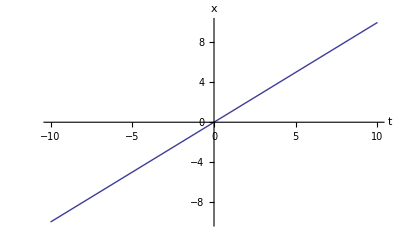

```mathematica
Plot[t,{t,-10,10},AxesLabel->{t,x}]
```

Example
4.3.9

```mathematica
F(y)=Pr(Y≤y)=Pr(2X≤y)=Pr(X≤y/2)=F(y/2)=∫_(-∞)^(y/2) 1/(1+y^2)ⅆy=1/2+ArcTan(y/2)
```

4.3-5

```mathematica
Ex[(X-c)^2]=Ex[(X-μ)^2+(μ-c)^2+2(X-μ)(μ-c)]=σ^2+(μ-c)^2
```

Theorem
4.4.4

```mathematica
D[(p ⅇ^t+1−p)^n,t]
```

ⅇ^t n p (1-p+ⅇ^t p)^(-1+n)

Theorem
4.4.6

4.4-4

```mathematica
En[X^2]-(En[X])^2
```

Example
4.6.3

```mathematica
∫_0^1 (∫_0^1 (2x y+1/2)x^2 ⅆx)ⅆy
```

5/12

Example
4.7.2

```mathematica
2/(2+30+15+5)//N
```

0.0384615

Example
4.7.4

```mathematica
1*0.536+2*0.280+3*0.084
```

1.348

Example
4.7.8

5.2-1

```mathematica
Pr(X=1)=1/3
```

5.2-2

```mathematica
(x-b);(x-b)/(a-b)
```

```mathematica
p^((x-b)/(a-b))(1-p)^((x-a)/(b-a))
```

5.2-9

```mathematica
(p Binomial[n-1,k-1] p^(k-1)(1-p)^(n-k))/(Binomial[n,k] p^k(1-p)^(n-k))=k/n
```

5.2-11

```mathematica
n p(1-p)+(n p)^2-n p=(n p)^2-n p^2
```

5.2-12

```mathematica
(Binomial[n,x] p^x(1-p)^(n-x))/(Binomial[n,x-1] p^(x-1)(1-p)^(n-x+1))=((n!)/((x)!(n-x)!))/((n!)/((x-1)!(n-x+1)!))p/(1-p)=(n-x+1)/x p/(1-p)
```

```mathematica
Solve[(n-x+1)/x p/(1-p)==1,x]
```

{{x→p+n p}}

```mathematica
Table[PDF[BinomialDistribution[100,0.555],i],{i,51,60}]
```

{0.0529464,0.0622246,0.0702846,0.0762953,0.079584,0.0797596,0.0767881,0.0710015,0.0630373,0.0537234}

5.2-15

```mathematica
10+100+1000=1110;
```

```mathematica
(0.0198)^100
```

4.64001×10^-171

Theorem
5.3.2

```mathematica
(A/(A+B))-(A/(A+B))^2//Simplify
```

(A B)/(A+B)^2

```mathematica
Ex(X Y)=(A/(A+B))((A-1)/(A+B-1))
```

```mathematica
(A/(A+B))((A-1)/(A+B-1))-(A/(A+B))^2//Simplify
```

-(A B)/((-1+A+B) (A+B)^2)

```mathematica
n(A B)/(A+B)^2+n(n-1)(-(A B)/((-1+A+B) (A+B)^2))//Simplify
```

(A B (A+B-n) n)/((-1+A+B) (A+B)^2)

```mathematica
D[Log[1+Subscript[a, n]],Subscript[a, n]]
D[Log[1+Subscript[a, n]],{Subscript[a, n],2}]
```

1/(1+a_n)

-1/(1+a_n)^2

```mathematica
Series[Log[1+Subscript[a, n]],{Subscript[a, n],0,2}]
```

a_n-a_n^2/2+O[a_n]^3

```mathematica
Subscript[a, n]+(-1/(1+z)^2)/2 Subscript[a, n]^2=Subscript[a, n]-1/(2(1+z)^2)Subscript[a, n]^2
```

Theorem
5.3.4

```mathematica
(({{A}, {x}}) ({{B}, {n-x}}))/({{A+B}, {n}})=(A! B!)/(((A+B)! (x! (A-x)!) ((n-x)! (B-n+x)!))/(n! (A+B-n)!))
```

```mathematica
(Subscript[A, T]/(Subscript[A, T]-x))^(Subscript[A, T]-x+1/2)=(x/(Subscript[A, T]-x)+1)^(Subscript[A, T]-x+1/2)
```

```mathematica
Subscript[B, T]/(Subscript[B, T]-n+x)=(n-x)/(Subscript[B, T]-n+x)+1
```

5.3-1

```mathematica
Binomial[24,1]/Binomial[34,11]//N
```

8.38874×10^-8

Example
5.4.1

```mathematica
Binomial[3600, x] ((0.00125^x)[1-0.00125])^(3600-x);
```

```mathematica
x=1;Binomial[3600, x] ((0.00125^x)[1-0.00125])^(3600-x);
```

```mathematica
PDF[BinomialDistribution[3600,0.00125],1]//N
```

0.0499124

```mathematica
PDF[PoissonDistribution[3600*0.00125],1]//N
```

0.0499905

```mathematica
3600*0.00125
```

4.5

```mathematica
CDF[PoissonDistribution[4.5`100],20]
```

0.999999985777130033061075232534948196424055829006002260694820011485035496899947831175937211334012606

70 rule

```mathematica
(1+x/n)^n=ⅇ^x=2
```

```mathematica
x=Log[2]//N
```

0.693147

```mathematica
Clear[x];Solve[ⅇ^x==3,x]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.09861}}

5.4-16

```mathematica
({{n}, {k}}) ((t λ)/n)^k (1-(t λ)/n)^(n-k)=(n!)/(k! (n-k)!)((t λ)/n)^k (1-(t λ)/n)^(n-k)
```

Theorem
5.5.4

```mathematica
D[p/(1-(1-p)ⅇ^t),t]
```

(ⅇ^t (1-p) p)/((1-ⅇ^t (1-p))^2)

```mathematica
%/.t->0
```

(1-p)/p

```mathematica
D[p/(1-(1-p)ⅇ^t),{t,2}]//Simplify
```

(ⅇ^t (-1+ⅇ^t (-1+p)) (-1+p) p)/((1+ⅇ^t (-1+p))^3)

```mathematica
%/.t->0
```

((-2+p) (-1+p))/p^2

```mathematica
((-2+p) (-1+p))/p^2-((1-p)/p)^2//Simplify
```

(1-p)/p^2

5.5-13

```mathematica
Pr(x≥t+h|x≥t)
```

```mathematica
Log[1-F(t-1)]=t Log[1-F(0)]
1-F(t-1)=(1-F(0))^t
1-F(t)=(1-F(0))^(t+1)
Pr(x=t)=(1-F(0))^t-(1-F(0))^(t+1)=(1-F(0))^t F(0)=(1-Pr(x=0))^t Pr(x=0)
```

Theorem
5.6.2

```mathematica
t x-((x-μ)^2//Expand)/(2 σ^2)
```

t x-(x^2-2 x μ+μ^2)/(2 σ^2)

```mathematica
t x-(x^2-2 x μ+μ^2)/(2 σ^2)//Together
```

(-x^2+2 x μ-μ^2+2 t x σ^2)/(2 σ^2)

```mathematica
Collect[-x^2+2 x μ-μ^2+2 t x σ^2,x]
```

-x^2-μ^2+x (2 μ+2 t σ^2)

```mathematica
(-x^2+x (2 μ+2 t σ^2)-((μ+t σ^2))^2+((μ+t σ^2))^2-μ^2)/(2 σ^2)
```

```mathematica
(((μ+t σ^2))^2-μ^2)/(2 σ^2)//Expand
```

t μ+(t^2 σ^2)/2

Example
5.6.10

```mathematica
(1+r/n)^(n u)
```

```mathematica
Log(q/Subscript[s, 0])
```

```mathematica
ax^2+bx+c
b^2-4a c=0
```

```mathematica
(ax^2+bx+(b/2)^2/a)
```

```mathematica
-z^2/2+σ u^(1/2)z+(σ^2 u)/-2
```

5.6-24

```mathematica
∑_(i=1)^n Subscript[a, i](x-Subscript[b, i])^2+c x
```

```mathematica
∑_(i=1)^n Subscript[a, i](Subscript[b, i]-(∑_(i=1)^n Subscript[a, i] Subscript[b, i])/(∑_(i=1)^n Subscript[a, i]))^2=∑_(i=1)^n Subscript[a, i](Subscript[b, i]-(∑_(i=1)^n Subscript[a, i] Subscript[b, i])/(∑_(i=1)^n Subscript[a, i]))^2
```

```mathematica
∑_(i=1)^n Subscript[a, i] Expand[(Subscript[b, i]-(∑_(i=1)^n Subscript[a, i] Subscript[b, i])/(∑_(i=1)^n Subscript[a, i]))^2]
```

∑_(i=1)^n a_i (b_i^2-(2 b_i ∑_(i=1)^n a_i b_i)/(∑_(i=1)^n a_i)+((∑_(i=1)^n a_i b_i)^2)/((∑_(i=1)^n a_i)^2))

```mathematica
∑_(i=1)^n Subscript[a, i] Expand[((∑_(i=1)^n Subscript[a, i] Subscript[b, i]-c/2)/(∑_(i=1)^n Subscript[a, i]))^2]
```

∑_(i=1)^n a_i (c^2/(4 (∑_(i=1)^n a_i)^2)-(c ∑_(i=1)^n a_i b_i)/((∑_(i=1)^n a_i)^2)+((∑_(i=1)^n a_i b_i)^2)/((∑_(i=1)^n a_i)^2))

5.7.7

```mathematica
x^(-1/2)d x=2d x^(1/2)
```

Example
5.7.3

```mathematica
Integrate[x z ⅇ^(-z x),{x,0,∞},Assumptions->z>0]
```

1/z

```mathematica
1/z n
```

5.7-13

```mathematica
β =1/80;∫_100^t β ⅇ^(-β x)ⅆ□
```

```mathematica
β =1/80;t=40;
ⅇ^(-β 4t)
1-( ⅇ^(-β t))^5
```

1/ⅇ^2

1-1/ⅇ^(5/2)

5.7-15

```mathematica
β =1/80;t=10;
ⅇ^(-β 4t)
( ⅇ^(-β t))^4( ⅇ^(-β t))^3( ⅇ^(-β t))^2( ⅇ^(-β t))^1
```

1/(√ⅇ)

1/ⅇ^(5/4)

5.7-16

```mathematica
(α Subscript[x, 0]^α)/x^(α+1),x>Subscript[x, 0]
```

```mathematica
Y=Log[X/Subscript[x, 0]];X=Subscript[x, 0] ⅇ^Y;(α Subscript[x, 0]^α)/((Subscript[x, 0] ⅇ^y)^(α+1))Subscript[x, 0] ⅇ^y=(α Subscript[x, 0]^α)/((Subscript[x, 0] ⅇ^y)^α)=α ⅇ^(-α y),y>0
```

5.7-17

```mathematica
ψ(t)=ⅇ^(μ t +1/2 σ^2 t^2)
Y=x-μ;Subscript[ψ, Y](t)=ⅇ^(1/2 σ^2 t^2)
```

```mathematica
D[ⅇ^(1/2 σ^2 t^2),{t,10}]
D[ⅇ^(1/2 σ^2 t^2),{t,20}]
```

945 ⅇ^((t^2 σ^2)/2) σ^10+4725 ⅇ^((t^2 σ^2)/2) t^2 σ^12+3150 ⅇ^((t^2 σ^2)/2) t^4 σ^14+630 ⅇ^((t^2 σ^2)/2) t^6 σ^16+45 ⅇ^((t^2 σ^2)/2) t^8 σ^18+ⅇ^((t^2 σ^2)/2) t^10 σ^20

654729075 ⅇ^((t^2 σ^2)/2) σ^20+6547290750 ⅇ^((t^2 σ^2)/2) t^2 σ^22+9820936125 ⅇ^((t^2 σ^2)/2) t^4 σ^24+5237832600 ⅇ^((t^2 σ^2)/2) t^6 σ^26+1309458150 ⅇ^((t^2 σ^2)/2) t^8 σ^28+174594420 ⅇ^((t^2 σ^2)/2) t^10 σ^30+13226850 ⅇ^((t^2 σ^2)/2) t^12 σ^32+581400 ⅇ^((t^2 σ^2)/2) t^14 σ^34+14535 ⅇ^((t^2 σ^2)/2) t^16 σ^36+190 ⅇ^((t^2 σ^2)/2) t^18 σ^38+ⅇ^((t^2 σ^2)/2) t^20 σ^40

```mathematica
∫_(-∞)^∞ x^(2n)/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)x^2)ⅆx=∫_(-∞)^∞ x^(2n)/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)x^2)ⅆx
```

```mathematica
v=x^2;ⅆ v=2x ⅆ x;2*1/2∫_0^∞ v^(n-1/2)/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)v)ⅆv=1/((2 π)^(1/2)σ)(Γ(n+1/2))/((1/(2 σ^2))^(n+1/2))
=1/(π)^(1/2)(Γ(n+1/2))/((1/(2 σ^2))^(n))=1/(π)^(1/2)Γ(n+1/2)(2 σ^2)^(n)
```

```mathematica
1/(π)^(1/2)Gamma[5+1/2] 2^5 σ^10
1/(π)^(1/2)Gamma[10+1/2] 2^10 σ^20
```

945 σ^10

654729075 σ^20

```mathematica
∫_-1^1 x^2 ⅆx
```

5.7-18

```mathematica
(β ⅇ^(-β x))/ⅇ^(-β x)
```

5.7-21

```mathematica
(ⅇ^(-β x) x^(α-1) β^α)/Γ[α];∫_0^∞ (ⅇ^(-β x) x^(α-1) β^α)/Γ[α] 1/x ⅆx=β^α/Γ[α]∫_0^∞ ⅇ^(-β x) x^(α-1) 1/x ⅆx=β^α/Γ[α] Γ[α-1]/β^(α-1)=β/(α-1)
```

```mathematica
β^α/Γ[α] Γ[α-2]/β^(α-2)=β^2/((α-1)(α-2));β^2/((α-1)(α-2))-β^2/(α-1)^2
```

5.7-22

```mathematica
f(β,x)=γ^α/(Γ(α))β^(α-1)ⅇ^(-γ β)(ⅇ^-β β^x)/(x!)=γ^α/(Γ(α)x!)β^(x+α-1)ⅇ^(-(γ +1)β)
```

```mathematica
Subscript[f, 1](β)=∫_0^∞ γ^α/(Γ(α))β^(α-1)ⅇ^(-γ β)(ⅇ^-β β^x)/(x!)ⅆβ=∫_0^∞ γ^α/(Γ(α)x!)β^(x+α-1)ⅇ^(-(γ +1)β)ⅆβ=γ^α/(Γ(α)x!)(Γ(x+α))/(γ +1)^(x+α)
```

```mathematica
g(β|X=x)=(β^(x+α-1)ⅇ^(-(γ +1)β))/((Γ(x+α))/(γ +1)^(x+α))=(γ +1)^(x+α)/(Γ(x+α))β^(x+α-1)ⅇ^(-(γ +1)β)
```

5.7-23

```mathematica
Pr(x≥t+h|x≥t)
```

```mathematica
ℓ(k t)=k ℓ(t)
ℓ(m t/m)=m ℓ(t/m)
```

```mathematica
ℓ(c t)=c ℓ (t)
ℓ(c t)=Underscript[Lim, x->c] ℓ(x t)=Underscript[Lim, x->c] x ℓ(t)=c ℓ (t)
```

```mathematica
c=Log[1-F(1)]
Log[1-F(t)]=c t
1-F(t)=ⅇ^(c t)
F(t)=1-ⅇ^(c t)
```

5.7-24

```mathematica
Subscript[S, 0]=ⅇ^(-r u)Ex(Subscript[S, u])=ⅇ^(-r u)Ex(Subscript[S, 0] ⅇ^(μ u+Subscript[W, u]))
X=ⅇ^Subscript[W, u] ;Y=Log[X];Subscript[ψ, Y](t)=Ex(ⅇ^(t Y))=(β/(β-t))^(α u);
Subscript[ψ, Y](1)=Ex(X)=(β/(β-1))^(α u)
ⅇ^(-r u)Ex(Subscript[S, 0] ⅇ^(μ u+Subscript[W, u]))=Subscript[S, 0] ⅇ^(-r u+μ u)(β/(β-1))^(α u)
```

```mathematica
ⅇ^(-r u+μ u)(β/(β-1))^(α u)==1;-r u+μ u+Log[(β/(β-1))^(α u)]==0;
μ==1/u(r u-α u Log[β/(β-1)])=r -α  Log[β/(β-1)]
```

```mathematica
Subscript[S, 0] ⅇ^(μ u+Subscript[W, u])>q;ⅇ^(μ u+Subscript[W, u])>q/Subscript[S, 0];μ u+Subscript[W, u]>Log[q/Subscript[S, 0]];
Subscript[W, u]>Log[q/Subscript[S, 0]]-μ u;
Subscript[W, u]>Log[q/Subscript[S, 0]]-(r -α  Log[β/(β-1)]) u;
Subscript[W, u]>Log[q/Subscript[S, 0]]+u α  Log[β/(β-1)]-r u;
ⅇ^(-r u)Ex(h(Subscript[S, u]))=ⅇ^(-r u)∫_c^∞ (Subscript[S, 0] ⅇ^(μ u+z)-q)(β^α/(Γ(α))z^(α-1)ⅇ^(-β z))ⅆz=ⅇ^(-r u)∫_c^∞ (Subscript[S, 0] ⅇ^((r -α  Log[β/(β-1)]) u+z)-q)(β^α/(Γ(α))z^(α-1)ⅇ^(-β z))ⅆz=
ⅇ^(-r u)∫_c^∞ (Subscript[S, 0] ⅇ^((r -α  Log[β/(β-1)]) u+z))(β^α/(Γ(α))z^(α-1)ⅇ^(-β z))ⅆz-ⅇ^(-r u)∫_c^∞ q(β^α/(Γ(α))z^(α-1)ⅇ^(-β z))ⅆz=
ⅇ^(-r u)(Subscript[S, 0] ⅇ^((r -α  Log[β/(β-1)]) u))∫_c^∞ (β^α/(Γ(α))x^(α-1)ⅇ^(-(β -1)z))ⅆz-ⅇ^(-r u)∫_c^∞ q(β^α/(Γ(α))z^(α-1)ⅇ^(-β z))ⅆz
```

```mathematica
ⅇ^(-r u)(Subscript[S, 0] ⅇ^(μ u))∫_c^∞ (β^α/(Γ(α))x^(α-1)ⅇ^(-(β -1)z))ⅆz=
ⅇ^(-r u)(Subscript[S, 0] ⅇ^((r -α  Log[β/(β-1)]) u))∫_c^∞ (β^α/(Γ(α))x^(α-1)ⅇ^(-(β -1)z))ⅆz=
((β-1)/β)^(α u)∫_c^∞ (β^(α u)/(Γ(α u))x^(α u-1)ⅇ^(-(β -1)z))ⅆz=
```

```mathematica
∫_c^∞ (β^α/(Γ(α))z^(α-1)ⅇ^(-β z))ⅆz
∫_c^∞ (1^α/(Γ(α))z^(α-1)ⅇ^(- z))ⅆz
```

Example
5.8.3

```mathematica
β=51.5;α=3.785β;Mean[BetaDistribution[α,β]]
```

0.791014

```mathematica
β=51.5;α=3.785β;CDF[BetaDistribution[α,β],0.6328]//N
```

3.2631×10^-8

```mathematica
β=51.5;α=3.785β;CDF[BetaDistribution[α+100,β+120],0.6328]//N
```

0.505344

```mathematica
BetaDistribution[α,β]
```

Theorem
5.10.1

```mathematica
Subscript[z, 1]=(Subscript[x, 1]-Subscript[μ, 1])/Subscript[σ, 1];Subscript[z, 2]=1/((1-ρ^2)^(1/2))((Subscript[x, 2]-Subscript[μ, 2])/Subscript[σ, 2]-ρ(Subscript[x, 1]-Subscript[μ, 1])/Subscript[σ, 1]);
Subscript[z, 1]^2
 Subscript[z, 2]^2
```

(x_1-μ_1)^2/σ_1^2

(-(ρ (x_1-μ_1))/σ_1+(x_2-μ_2)/σ_2)^2/(1-ρ^2)

```mathematica
(-(ρ (Subscript[x, 1]-Subscript[μ, 1]))/Subscript[σ, 1]+(Subscript[x, 2]-Subscript[μ, 2])/Subscript[σ, 2])^2/(1-ρ)
```

```mathematica
Expand[(Subscript[y, 1]+Subscript[y, 2])^2]/(1-ρ)/.{Subscript[y, 1]->-(ρ (Subscript[x, 1]-Subscript[μ, 1]))/Subscript[σ, 1],Subscript[y, 2]->(Subscript[x, 2]-Subscript[μ, 2])/Subscript[σ, 2]}
```

((ρ^2 (x_1-μ_1)^2)/σ_1^2+(x_2-μ_2)^2/σ_2^2-(2 ρ (x_1-μ_1) (x_2-μ_2))/(σ_1 σ_2))/(1-ρ)

```mathematica
<<MultivariateStatistics`
Plot3D[PDF[MultinormalDistribution[{0,0},{{2,0},{0,2}}],{x,y}],{x,-4,4},{y,-4,4},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},AxesLabel->Automatic]
```

-Graphics3D-

5.10-14

```mathematica
PDF[NormalDistribution[μ,σ]]
```

(ⅇ^(-(-μ+#1)^2/(2 σ^2)))/(√(2 π) σ)&

```mathematica
(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)
```

```mathematica
1/(√(2 π) τ)ⅇ^(-(y-(a x+b))^2/(2 τ^2))
```

```mathematica
1/(√(2 π) τ)ⅇ^(-(y-(a x+b))^2/(2 τ^2))1/(√(2 π) σ)ⅇ^(-(x-μ)^2/(2 σ^2))=
```

```mathematica
1/(2 π τ σ)Exp[-(y-(a x+b))^2/(2 τ^2)-(x-μ)^2/(2 σ^2)]
```

```mathematica
(Subscript[x, 1]-Subscript[μ, 1])^2/Subscript[σ, 1]^2+(Subscript[x, 2]-Subscript[μ, 2])^2/Subscript[σ, 2]^2-(2 ρ (Subscript[x, 1]-Subscript[μ, 1]) (Subscript[x, 2]-Subscript[μ, 2]))/(Subscript[σ, 1] Subscript[σ, 2])=
(Subscript[x, 1]-Subscript[μ, 1])^2/Subscript[σ, 1]^2+(Subscript[x, 2]-Subscript[μ, 2])^2/Subscript[σ, 2]^2-(2 ρ (Subscript[x, 1]-Subscript[μ, 1]) (Subscript[x, 2]-Subscript[μ, 2]))/(Subscript[σ, 1] Subscript[σ, 2])+((ρ  (Subscript[x, 2]-Subscript[μ, 2]))/Subscript[σ, 2])^2-((ρ  (Subscript[x, 2]-Subscript[μ, 2]))/Subscript[σ, 2])^2
```

```mathematica
-(1/(2(1-ρ^2)))[((Subscript[x, 1]-Subscript[μ, 1])/Subscript[σ, 1]-(ρ  (Subscript[x, 2]-Subscript[μ, 2]))/Subscript[σ, 2])^2-((ρ  (Subscript[x, 2]-Subscript[μ, 2]))/Subscript[σ, 2])^2+(Subscript[x, 2]-Subscript[μ, 2])^2/Subscript[σ, 2]^2]=
-(1/(2(1-ρ^2)))[((Subscript[x, 1]-Subscript[μ, 1])/Subscript[σ, 1]-(ρ  (Subscript[x, 2]-Subscript[μ, 2]))/Subscript[σ, 2])^2+(Subscript[x, 2]-Subscript[μ, 2])^2/Subscript[σ, 2]^2(1-ρ^2 )]=
-(1/(2(1-ρ^2)))[((Subscript[x, 1]-Subscript[μ, 1])/Subscript[σ, 1]-(ρ  (Subscript[x, 2]-Subscript[μ, 2]))/Subscript[σ, 2])^2+(Subscript[x, 2]-Subscript[μ, 2])^2/Subscript[σ, 2]^2(1-ρ^2 )]=
-1/(2(1-ρ^2))((Subscript[x, 1]-Subscript[σ, 1] ρ/Subscript[σ, 2] Subscript[x, 2]+Subscript[σ, 1](ρ Subscript[μ, 2])/Subscript[σ, 2]-Subscript[μ, 1])/Subscript[σ, 1])^2
```

```mathematica
2(1-ρ^2)Subscript[σ, 1]^2=2 τ^2
(1-ρ^2)Subscript[σ, 1]^2=τ^2
Subscript[σ, 1] ρ =Subscript[σ, 2]
```

5.10-15

```mathematica
Det|({{1, 0}, {-1, n}})|=n
```

```mathematica
1/(2π σ^2 √(n-1))Exp[-1/2(((Subscript[x, i]-μ)/σ)^2((n Subscript[x, n]^--Subscript[x, i]-(n-1)μ)/(√(n-1)σ))^2)]n=
1/(2π σ^2 √(n-1)1/n) Exp[-1/2(((Subscript[x, i]-μ)/σ)^2-(((n Subscript[x, n]^--n μ)-(Subscript[x, i]-μ))/(√(n-1)σ))^2)]=
1/(2π σ^2 √(1/n)√(1-1/n)) Exp[-1/2(((Subscript[x, i]-μ)/σ)^2+((n(Subscript[x, n]^--μ))/(√(n-1)σ))^2+((Subscript[x, i]-μ)/(√(n-1)σ))^2-(2n(Subscript[x, n]^--μ)(Subscript[x, i]-μ))/(√(n-1)σ  )^2)]=
1/(2π σ^2 √(1/n)√(1-1/n)) Exp[-1/2((n(Subscript[x, i]-μ)^2)/((n-1)σ^2)+(n^2(Subscript[x, n]^--μ)^2)/((n-1)σ^2)-(2n(Subscript[x, n]^--μ)(Subscript[x, i]-μ))/((n-1)σ^2))]=
1/(2π σ^2 √(1/n)√(1-1/n)) Exp[-1/(2(1-1/n))(((Subscript[x, i]-μ)/σ)^2+((Subscript[x, n]^--μ)/(σ/(√n)))^2-1/(√n)(2(Subscript[x, n]^--μ)(Subscript[x, i]-μ))/(σ^2/(√n)))]
```

```mathematica
1/(√(2π) σ/(√n))Exp[-1/2((Subscript[x, n]^--μ)/(σ/(√n)))^2]
```

```mathematica
1/(√(2π) σ √(1-1/n))Exp[-1/2((n(Subscript[x, i]-μ)^2)/((n-1)σ^2)+(n^2(Subscript[x, n]^--μ)^2)/((n-1)σ^2)-(2n(Subscript[x, n]^--μ)(Subscript[x, i]-μ))/((n-1)σ^2)-(n(Subscript[x, n]^--μ)^2)/σ^2)]=
1/(√(2π) σ √(1-1/n))Exp[-1/2((n(Subscript[x, i]-μ)^2)/((n-1)σ^2)+(n(Subscript[x, n]^--μ)^2)/((n-1)σ^2)-(2n(Subscript[x, n]^--μ)(Subscript[x, i]-μ))/((n-1)σ^2))]=
1/(√(2π) σ √(1-1/n))Exp[-1/2((((Subscript[x, i]-μ)-(Subscript[x, n]^--μ))^2)/((1-1/n)σ^2))]
```

Theorem
6.2.7

```mathematica
Pr(X≥t)=Pr(ⅇ^(s X)≥ⅇ^(s t))<=Ex[ⅇ^(s X)]/ⅇ^(s t)
```

6.2-10

```mathematica
Clear[μ];Ex[(Subscript[Z, n]-b)^2]=Subscript[σ, n]^2+(Subscript[μ, n]-b)^2
```

6.2-14

```mathematica
Pr(X=1)=p;μ=p;σ^2=(1-p)p^2+p(1-p)^2=(1-p)p
```

```mathematica
D[(1-p)p,p]
```

1-2 p

6.2-18

```mathematica
Pr(X≥t)=Pr(ⅇ^(s X)≥ⅇ^(s t))<=Ex[ⅇ^(s X)]/ⅇ^(s t)
```

6.2-24

```mathematica
∫_0^(1/n) n^2 ⅆx=n
```

Example
6.3.8

```mathematica
|(2(Subscript[X, n]^-)^(1/2)-2 θ^(1/2))n^(1/2)|<c;2(Subscript[X, n]^-)^(1/2)-c/n^(1/2)<2 θ^(1/2);((Subscript[X, n]^-)^(1/2)-1/2 c/n^(1/2))^2<θ
```

```mathematica
|(n^(1/2)(Subscript[X, n]^--θ))/θ|<c;(Subscript[X, n]^--θ)<c/n^(1/2)θ;Subscript[X, n]^-<(c/n^(1/2)+1)θ
```

6.3-1

```mathematica
Ex(Subscript[X, i])=4,σ=5/12
```

```mathematica
Pr(Z≥250)=Pr((Z-60*4)/(√60*5/12)≥(250-60*4)/(√60*5/12))
```

```mathematica
(250-60*4)/(√60*5/12)
```

4 √(3/5)

```mathematica
1-CDF[NormalDistribution[0,1],4 √(3/5)]//N
```

0.000972887

6.3-2

```mathematica
Ex(Subscript[X, i])=0.25,Var(Subscript[X, i])=0.25-0.25^2
```

6.3-3

```mathematica
μ=5;σ^2=5;
```

```mathematica
(5.5-5)/((√5)/(√125))
```

2.5

```mathematica
Pr((Subscript[x̄, n]-5)/((√5)/(√125))≤(5.5-5)/((√5)/(√125)))=Pr((Subscript[x̄, n]-5)/((√5)/(√125))≤2.5)
```

```mathematica
CDF[NormalDistribution[0,1],2.5]//N
```

0.99379

6.3-4

```mathematica
Pr((|Subscript[x̄, n]-μ|)/(3/(√n))≤0.3/(3/(√n)))
```

```mathematica
Solve[0.3/(3/(√n))==1.96,n]
```

{{n→384.16}}

6.3-5

```mathematica
Pr((Subscript[x̄, n]-0.1)/((√(0.1-0.1^2))/(√n))≤(0.13-0.1)/((√(0.1-0.1^2))/(√n)))
```

```mathematica
Solve[(0.13-0.1)/((√(0.1-0.1^2))/(√n))==2.33,n]
```

{{n→542.89}}

6.3-6

```mathematica
Pr((Z-(10*0.3+15*0.2+20*0.1))/(10*(0.3-0.3^2)+15*(0.2-0.2^2)+20*(0.1-0.1^2))>=(12-(10*0.3+15*0.2+20*0.1))/(10*(0.3-0.3^2)+15*(0.2-0.2^2)+20*(0.1-0.1^2)))
```

```mathematica
(12-(10*0.3+15*0.2+20*0.1))/(10*(0.3-0.3^2)+15*(0.2-0.2^2)+20*(0.1-0.1^2))
```

0.634921

```mathematica
1-CDF[NormalDistribution[0,1],0.6349]//N
```

0.262747

6.3-7

```mathematica
{(4-4.5)/((√(∑_(i=0)^9 1/10(i-4.5)^2))/4),(6-4.5)/((√(∑_(i=0)^9 1/10(i-4.5)^2))/4)}
```

{-0.696311,2.08893}

```mathematica
Pr((4-4.5)/((√(∑_(i=0)^9 1/10(i-4.5)^2))/4)<=(Subscript[x̄, n]-4.5)/((√(∑_(i=0)^9 1/10(i-4.5)^2))/4)≤(6-4.5)/((√(∑_(i=0)^9 1/10(i-4.5)^2))/4))
```

```mathematica
CDF[NormalDistribution[0,1],2.0889]-CDF[NormalDistribution[0,1],-0.6963]//N
```

0.738521

6.3-12

```mathematica
(p ⅇ^t+1-p)^n=(1+p ⅇ^t-p)^n,ⅇ^((p ⅇ^t-p)n)
```

```mathematica
Limit[(1+p ⅇ^t-p)^n,n->∞]=ⅇ^( λ ⅇ^t-λ)
```

```mathematica
e^(λ(ⅇ^t-1))
```

6.3-13

```mathematica
α(x)=x^3,α^,(x)=3 x^2
```

```mathematica
n^(1/2)/(σ 3 θ^2)(Subscript[x̄, n]^3-θ^3),θ^3,(3σ θ^2)/n^(1/2)
```

6.4-1

```mathematica
Ex(Subscript[X, i])=1/4*2+1/2*1=1,Var(Subscript[X, i])=1/4*(2-1)^2+1/4=1/2
```

```mathematica
(33.5-30)/(√(30/2))
```

0.903696

```mathematica
Pr(Z≤33.5)=Pr((Z-30)/(√(30/2))≤(33.5-30)/(√(30/2)))=Pr((Z-30)/(√(30/2))≤0.9037)
```

```mathematica
CDF[NormalDistribution[0,1],0.9037]//N
```

0.816923

6.4-2

```mathematica
Ex(Subscript[X, i])=0.3,Var(Subscript[X, i])=0.3-0.3^2=0.21
```

```mathematica
Pr(3.5<=Z<=4.5)=Pr((3.5-4.5)/(√(15*0.21))<=(Z-4.5)/(√(15*0.21))<=(4.5-4.5)/(√(15*0.21)))
```

```mathematica
{(3.5-4.5)/(√(15*0.21)),(4.5-4.5)/(√(15*0.21))}
```

{-0.563436,0.}

```mathematica
CDF[NormalDistribution[0,1],0]-CDF[NormalDistribution[0,1],-0.5634]//N
```

0.213419

```mathematica
PDF[BinomialDistribution[15,0.3],4]
```

0.218623

6.5-5

```mathematica
∫_0^p 1/(√(x(1-x)))ⅆx=∫_0^(√p) 1/(z √(1-z^2))2zⅆz=∫_0^(√p) 2/(√(1-z^2))ⅆz=2ArcSin[√p]
```

```mathematica
z=√x;x=z^2;
```

```mathematica
D[2ArcSin[√x],x]
```

1/(√(1-x) √x)

7.2-3

```mathematica
(ⅇ^-λ λ^x)/(x!)
```

```mathematica
(ⅇ^-1.0 1.0^3)/(3!)0.4+(ⅇ^-1.5 1.5^3)/(3!)0.6
```

```mathematica
((ⅇ^-1.0 1.0^3)/(3!)0.4)/((ⅇ^-1.0 1.0^3)/(3!)0.4+(ⅇ^-1.5 1.5^3)/(3!)0.6)
```

0.245666

7.2-5

```mathematica
α/(α+β)=1/3,3α=α+β,2α=β
```

```mathematica
(α β)/((α+ β)^2(α+ β+1))=1/45,(α 2α)/((α+ 2α)^2(α+ 2α+1))=1/45,90 α^2=(3α)^2(3α+1),
10=(3α+1)
```

7.2-6

```mathematica
θ^3(1-θ)^5
```

```mathematica
(Γ(4+6))/(Γ(4)Γ(6))θ^3(1-θ)^5=(9!)/(3!5!)θ^3(1-θ)^5
```

```mathematica
∫_0^1 (9!)/(3!5!)θ^3(1-θ)^5 ⅆθ
```

1

7.2-7

```mathematica
θ^3(1-θ)^5(1−θ)
```

7.2-8

```mathematica
(Subscript[f, n](Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]... Subscript[x, n]|θ)Subscript[ξ, 0](θ))/(Subscript[g, n](Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]... Subscript[x, n]))
```

```mathematica
Subscript[ξ, 1](θ|Subscript[x, 1])=(Subscript[f, 1](Subscript[x, 1]|θ)ξ(θ))/(Subscript[g, 1](Subscript[x, 1]))
```

```mathematica
Subscript[ξ, 2](θ|Subscript[x, 1],Subscript[x, 2])=(Subscript[f, 2](Subscript[x, 2]|θ,Subscript[x, 1])Subscript[ξ, 1](θ|Subscript[x, 1]))/(Subscript[g, 2](Subscript[x, 2]|Subscript[x, 1]))=(Subscript[f, 2](Subscript[x, 2]|θ)Subscript[ξ, 1](θ|Subscript[x, 1]))/(Subscript[g, 2](Subscript[x, 2]))=(Subscript[f, 2](Subscript[x, 2]|θ)Subscript[f, 1](Subscript[x, 1]|θ)ξ(θ))/(Subscript[g, 2](Subscript[x, 2])Subscript[g, 1](Subscript[x, 1]))
```

7.2-9

```mathematica
θ^3(1-θ)^5
```

7.2-10

```mathematica
Subscript[f, 1](x,θ)=f(x|θ)ξ(θ)=1*1/10
```

```mathematica
Subscript[f, 2](12)=∫_11.5^12.5 f(12|θ)ξ(θ)ⅆθ=∫_11.5^12.5 1/10 ⅆθ=1/10
```

```mathematica
Subscript[f, 3](θ|12)=(Subscript[f, 1](12,θ))/(Subscript[f, 2](12))=1,θ∈[11.5,12.5]
```

7.2-11

```mathematica
f(x^(->)|θ)ξ(θ)=1*1/10,θ∈[11.2,11.4]
```

Example
7.3.3

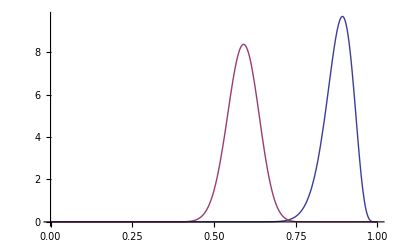

```mathematica
Needs["PlotLegends`"];Plot[{PDF[BetaDistribution[51,7],x],PDF[BetaDistribution[63,44],x]},{x,0,1},PlotRange->Full,PlotLegend->{"1", "2"}]
```

Theorem
7.3.3

```mathematica
(n/σ^2(Subscript[x, n]^-)+1/Subscript[ν, 0]^2 Subscript[μ, 0])/(n/σ^2+1/Subscript[ν, 0]^2)
```

Example
7.3.15

```mathematica
Subscript[v, 1]^2=(0.25 Subscript[v, 0]^2)/(0.25+n Subscript[v, 0]^2);1/Subscript[v, 1]^2=(0.25+n Subscript[v, 0]^2)/(0.25 Subscript[v, 0]^2)
```

7.3-1

```mathematica
Subscript[μ, 1]=(σ^2 Subscript[μ, 0]+n Subscript[ν, 0]^2 Subscript[x, n]^-)/(σ^2+n Subscript[ν, 0]^2)
```

```mathematica
Subscript[ν, 1]^2=(σ^2 Subscript[ν, 0]^2)/(σ^2+n Subscript[ν, 0]^2)
```

```mathematica
Solve[(100*0+20* x*0.125)/(100+20* x)==0.12,x]
```

{{x→120.}}

7.3-7

```mathematica
Subscript[μ, 1]=(2^2 68+10 1^2*69.5)/(2^2+10 1^2)
Subscript[ν, 1]=(2^2 1^2)/(2^2+10* 1^2)//N
```

69.0714

0.285714

7.3-15

```mathematica
x=θ^-1;∫_0^∞ θ^(-(α+1))ⅇ^(-β/θ)ⅆθ=∫_∞^0 x^(α+1)ⅇ^(-β x)(-1/x^2)ⅆx=∫_∞^0 x^(α+1)ⅇ^(-β x)(-1/x^2)ⅆx=
∫_∞^0 x^(α-1)ⅇ^(-β x)ⅆx
```

```mathematica
1/(√θ)ⅇ^(-1/2(x-μ)^2/θ)θ^(-(α+1))ⅇ^(-β/θ)=θ^(-(α+1+1/2))ⅇ^(-β/θ-1/2(x-μ)^2/θ)=θ^(-(α+1/2+1))ⅇ^(-(β-1/2(x-μ)^2)/θ)
```

```mathematica
α+1/2;(β-1/2(x-μ)^2);
```

7.3-21

```mathematica
θ^n ⅇ^(-θ y)θ^-1;n;y;μ=n/y;
```

7.4-1

```mathematica
α=2;β=1;α/(α+β)=2/3;∫_0^m 2xⅆx=1/2;m^2=1/2
```

7.4-4

```mathematica
α+∑_(i=1)^n Subscript[x, i];β+n-∑_(i=1)^n Subscript[x, i];(α+∑_(i=1)^n Subscript[x, i])/(α+β+n)=(α+β)/(α+β+n)α/(α+β)+n/(α+β+n)(∑_(i=1)^n Subscript[x, i])/n
```

7.4-6

```mathematica
α+∑_(i=1)^n Subscript[x, i];β+n;(α+∑_(i=1)^n Subscript[x, i])/(β+n)=β/(β+n)α/β+n/(β+n)(∑_(i=1)^n Subscript[x, i])/n
```

7.4-11

```mathematica
α+n;β+∑_(i=1)^n Subscript[x, i];SuperStar[δ]=(α+n)/(β+∑_(i=1)^n Subscript[x, i])=1/((β+∑_(i=1)^n Subscript[x, i])/(α+n))=1/(β/(α+n)+n/(α+n)(∑_(i=1)^n Subscript[x, i])/n)=1/(β/(α+n)+Ex(x))
```

7.4-13

```mathematica
(α Subscript[x, 0]^α)/θ^(α+1)1/θ=(α Subscript[x, 0]^α)/θ^(α+2)
```

```mathematica
∫_Subscript[x, 1]^∞ (α Subscript[x, 0]^α)/θ^(α+2)ⅆθ=-1/(α+1)(α Subscript[x, 0]^α)/θ^(α+1)|_Subscript[x, 1]^∞=-1/(α+1)(α Subscript[x, 0]^α)/Subscript[x, 1]^(α+1)=α/(α+1)Subscript[x, 0]^α/Subscript[x, 1]^(α+1)
```

```mathematica
Ex(θ)=∫_Subscript[x, 0]^∞ (α Subscript[x, 0]^α)/θ^(α+1)θⅆθ=∫_Subscript[x, 0]^∞ (α Subscript[x, 0]^α)/θ^α ⅆθ=α Subscript[x, 0]^α(-1/(α-1)1/θ^(α-1)|_Subscript[x, 0]^∞)=(α Subscript[x, 0]^α)/((α -1)Subscript[x, 0]^(α-1))=α/(α -1)Subscript[x, 0]
```

```mathematica
(α Subscript[x, 0]^α)/θ^(α+1)1/θ^n=(α Subscript[x, 0]^α)/θ^(α+1+n)
```

```mathematica
∫_Subscript[x, m]^∞ ((α+n) Subscript[x, m]^(α+n))/θ^(α+1+n)θⅆθ=(α +n)/(α+n -1)Subscript[x, m]
```

7.4-15

```mathematica
∫_q^∞ (θ-q)f(θ)ⅆθ+∫_(-∞)^q c(q-θ)f(θ)ⅆθ<=∫_d^∞ (θ-d)f(θ)ⅆθ+∫_(-∞)^d c(d-θ)f(θ)ⅆθ
```

```mathematica
(∫_x^∞ (θ-x)f(θ)ⅆθ+∫_(-∞)^x c(x-θ)f(θ)ⅆθ)'
```

```mathematica
(∫_x^∞ θ f(θ)ⅆθ-∫_x^∞ x f(θ)ⅆθ)'=-x f(x)-∫_x^∞ f(θ)ⅆθ-x(-f(x))=-∫_x^∞ f(θ)ⅆθ
```

```mathematica
(∫_(-∞)^x c x f(θ)ⅆθ+∫_(-∞)^x -c θ f(θ)ⅆθ)'=c∫_(-∞)^x f(θ)ⅆθ+c x f(x)-c x f(x)=c∫_(-∞)^x f(θ)ⅆθ
```

```mathematica
c∫_(-∞)^x f(θ)ⅆθ-∫_x^∞ f(θ)ⅆθ=0;c∫_(-∞)^x f(θ)ⅆθ=∫_x^∞ f(θ)ⅆθ;1/(1+c)
```

```mathematica
∫_q^∞ (θ-q)f(θ)ⅆθ+∫_(-∞)^q c(q-θ)f(θ)ⅆθ-∫_d^∞ (θ-d)f(θ)ⅆθ-∫_(-∞)^d c(d-θ)f(θ)ⅆθ=
∫_q^d (θ-q)f(θ)ⅆθ+(∫_d^∞ (θ-q)f(θ)ⅆθ-∫_d^∞ (θ-d)f(θ)ⅆθ)+(∫_(-∞)^q c(q-θ)f(θ)ⅆθ-∫_(-∞)^q c(d-θ)f(θ)ⅆθ)-∫_q^d c(d-θ)f(θ)ⅆθ=
∫_q^d ((θ-q)-c(d-θ))f(θ)ⅆθ+∫_d^∞ (d-q)f(θ)ⅆθ-∫_(-∞)^q c(d-q)f(θ)ⅆθ<=
∫_q^d c(d-q)f(θ)ⅆθ+∫_d^∞ (d-q)f(θ)ⅆθ-∫_(-∞)^q c(d-q)f(θ)ⅆθ
```

Example
7.5.4

```mathematica
(∑_(i=1)^n Subscript[x, i])1/θ+(n-∑_(i=1)^n Subscript[x, i])1/(1-θ)(-1)=0
```

```mathematica
(∑_(i=1)^n Subscript[x, i])(1-θ)=(n-∑_(i=1)^n Subscript[x, i])θ
```

Example
7.5.6

```mathematica
(-n/2 1/σ^2+1/(2(σ^2)^2)∑_(i=1)^n (Subscript[x, i]-Subscript[x, n]^-)^2)'=n/2 1/((σ^2)^2)-2 1/(2(σ^2)^3)∑_(i=1)^n (Subscript[x, i]-Subscript[x, n]^-)^2
```

Example
7.5.10

```mathematica
1/(√(2 π) σ)ⅇ^(-(x-μ)^2/(2 σ^2))
```

```mathematica
((1/σ)/(ⅇ^((x-μ)^2/(2 σ^2))))'=((-1/σ^2)/((ⅇ^((x-μ)^2/(2 σ^2)))(-2)(x-μ)^2/(2 σ^3)))
```

7.5-5

```mathematica
(ⅇ^-θ θ^x)/(x!)
```

```mathematica
((ⅇ^(-n θ)θ^(∑_(i=0)^n Subscript[x, i]))/(∏_(i=0)^n (Subscript[x, i]!)))'=-n(ⅇ^-θ θ^(∑_(i=0)^n Subscript[x, i]))/(∏_(i=0)^n (Subscript[x, i]!))+(ⅇ^-θ θ^((∑_(i=0)^n Subscript[x, i])-1))/(∏_(i=0)^n (Subscript[x, i]!))(∑_(i=0)^n Subscript[x, i]);θ=(∑_(i=0)^n Subscript[x, i])/n
```

7.5-7

```mathematica
β ⅇ^(-β x)
```

```mathematica
(β^n ⅇ^(-β ∑_(i=1)^n Subscript[x, i]))'=n β^(n-1)ⅇ^(-β ∑_(i=1)^n Subscript[x, i])+β^n ⅇ^(-β ∑_(i=1)^n Subscript[x, i])(-∑_(i=1)^n Subscript[x, i])=0;1/n∑_(i=1)^n Subscript[x, i]
```

7.5-9

```mathematica
θ x^(θ-1)
```

```mathematica
(θ^n(∏_(i=1)^n Subscript[x, i])^(θ-1))'=n θ^(n-1)(∏_(i=1)^n Subscript[x, i])^(θ-1)+θ^n(∏_(i=1)^n Subscript[x, i])^(θ-1)Log[∏_(i=1)^n Subscript[x, i]]
```

```mathematica
n=-θ̂ Log[∏_(i=1)^n Subscript[x, i]];θ̂=-n/Log[∏_(i=1)^n Subscript[x, i]]
```

7.5-13

```mathematica
-((Subscript[μ, x]-Subscript[x, 1])^2/Subscript[σ, x]^2+2ρ(Subscript[μ, x]-Subscript[x, 1])/Subscript[σ, x](Subscript[μ, y]-Subscript[y, 1])/Subscript[σ, y]+(Subscript[μ, y]-Subscript[y, 1])^2/Subscript[σ, y]^2)
```

```mathematica
((2∑_(i=1)^n (Subscript[μ, x]-Subscript[x, i]))/Subscript[σ, x]^2+2ρ 1/Subscript[σ, x](∑_(i=1)^n (Subscript[μ, y]-Subscript[y, i]))/Subscript[σ, y])=0;
((2∑_(i=1)^n (Subscript[μ, y]-Subscript[y, i]))/Subscript[σ, y]^2+2ρ 1/Subscript[σ, x](∑_(i=1)^n (Subscript[μ, x]-Subscript[x, i]))/Subscript[σ, y])=0;
```

```mathematica
(2/Subscript[σ, x]^2)(2/Subscript[σ, y]^2)-(2ρ 1/Subscript[σ, x] 1/Subscript[σ, y])^2
```

```mathematica
1/Subscript[σ, x]^n(-1/(2(1-ρ^2)))((-2)(Subscript[x, 1]-Subscript[μ, x])^2/Subscript[σ, x]^3-(-1)2ρ(Subscript[x, 1]-Subscript[μ, x])/Subscript[σ, x]^2(Subscript[y, 1]-Subscript[μ, y])/Subscript[σ, y])+(-n)1/Subscript[σ, x]^(n+1);
(-1/(2(1-ρ^2)))((-2)(Subscript[x, 1]-Subscript[μ, x])^2/Subscript[σ, x]^3-(-1)2ρ(Subscript[x, 1]-Subscript[μ, x])/Subscript[σ, x]^2(Subscript[y, 1]-Subscript[μ, y])/Subscript[σ, y])=n 1/Subscript[σ, x]^1;
(-1/(2(1-ρ^2)))((-2)(∑_(i=1)^n (Subscript[x, i]-Subscript[μ, x])^2)/Subscript[σ, x]^2-(-1)2ρ(∑_(i=1)^n [(Subscript[x, i]-Subscript[μ, x])(Subscript[y, i]-Subscript[μ, y])])/Subscript[σ, x]^1 1/Subscript[σ, y])=n
(-1/(2(1-ρ^2)))((-2)n+2 ρ^2 n)=n
```

Example7.6.11

```mathematica
μ=1/θ;σ^2=1/(n θ^2);(((σ^2)[α'(μ)])^2)/n=1/(n θ^2)(-1/(1/θ)^2)^2
```

7.6-3

```mathematica
∫_0^m β ⅇ^(-β x)ⅆx=1/2;1-ⅇ^(-β m)=1/2;ⅇ^(-β m)=1/2;-β m=-Log[2];m=Log[2]/β;m=Log[2](∑_(i=1)^n Subscript[x, i])/n
```

7.6-6

```mathematica
(X-μ)/σ≤1.65
```

7.6-11

```mathematica
θ-θ̂>ϵ
```

7.6-13

```mathematica
θ x^(θ-1);θ̂=-n/Log[∏_(i=1)^n Subscript[x, i]]=-n/(∑_(i=1)^n Log[Subscript[x, i]])
```

```mathematica
Y=Log[X];θ (ⅇ^(y())^(θ-1))ⅇ^y=θ ⅇ^(θ y);∫_(-∞)^0 θ yⅇ^(θ y)ⅆy=yⅇ^(θ y)|-∫_(-∞)^0 ⅇ^(θ y)ⅆy=-1/θ ⅇ^(θ y)|=-1/θ
```

7.6-18

```mathematica
Subscript[m, 1]=p;1/n∑_(i=1)^n Subscript[x, i]=p
```

7.6-19

```mathematica
Subscript[m, 1]=1/n∑_(i=1)^n Subscript[x, i]=1/β
```

7.6-19

```mathematica
Subscript[m, 1]=1/n∑_(i=1)^n Subscript[x, i]=μ;Subscript[m, 2]=1/n∑_(i=1)^n Subscript[x, i]^2=σ^2+μ^2;σ^2=1/n∑_(i=1)^n Subscript[x, i]^2-(1/n∑_(i=1)^n Subscript[x, i])^2
```

```mathematica
1/n∑_(i=1)^n (Subscript[x, i]-1/n∑_(i=1)^n Subscript[x, i])^2=1/n∑_(i=1)^n Subscript[x, i]^2+1/n n(1/n∑_(i=1)^n Subscript[x, i])^2-1/n 2∑_(i=1)^n (Subscript[x, i] 1/n∑_(i=1)^n Subscript[x, i])
```

7.6-20

```mathematica
Subscript[m, 1]=1/n∑_(i=1)^n Subscript[x, i]=λ
```

7.6-21

```mathematica
Subscript[m, 1]=1/n∑_(i=1)^n Subscript[x, i]=μ;Subscript[m, 2]=1/n∑_(i=1)^n Subscript[x, i]^2=σ^2+μ^2;σ^2=1/n∑_(i=1)^n Subscript[x, i]^2+(1/n∑_(i=1)^n Subscript[x, i])^2=1/n(∑_(i=1)^n Subscript[x, i]^2-1/n(∑_(i=1)^n Subscript[x, i])^2)=1/n∑_(i=1)^n (Subscript[x, i]-1/n∑_(i=1)^n Subscript[x, i])^2
```

7.6-24

```mathematica
1/(√(2 π) σ)ⅇ^(-(x-μ)^2/(2 σ^2))
```

```mathematica
1/(√(2 π) (Subscript[σ, 2](1-ρ^2)^(1/2)))Exp[-(y-(Subscript[μ, 2]+ρ Subscript[σ, 2]((x-Subscript[μ, 1])/Subscript[σ, 1])))^2/(2  (Subscript[σ, 2](1-ρ^2)^(1/2))^2)] 1/(√(2 π) Subscript[σ, 1])ⅇ^(-(x-Subscript[μ, 1])^2/(2 Subscript[σ, 1]^2))
```

```mathematica
-(ρ Subscript[σ, 2]((x-Subscript[μ, 1])/Subscript[σ, 1]))^2/(2  (Subscript[σ, 2](1-ρ^2)^(1/2))^2)-(x-Subscript[μ, 1])^2/(2 Subscript[σ, 1]^2)
```

```mathematica
∑_(i=1)^n Subscript[y, i]=∑_(i=1)^n (Subscript[μ, 2]+ρ Subscript[σ, 2]((Subscript[x, i]-Subscript[μ, 1])/Subscript[σ, 1]))=∑_(i=1)^n Subscript[μ, 2]+(ρ Subscript[σ, 2]((∑_(i=1)^n Subscript[x, i]-∑_(i=1)^n Subscript[μ, 1])/Subscript[σ, 1]))
```

```mathematica
α=Subscript[μ, 2]-ρ Subscript[σ, 2] Subscript[μ, 1]/Subscript[σ, 1];β=(ρ Subscript[σ, 2])/Subscript[σ, 1];α=Subscript[μ, 2]-β Subscript[μ, 1];∑_(i=1)^n Subscript[y, i]=∑_(i=1)^n (α+β Subscript[x, i])
```

```mathematica
Subscript[σ, 2,1]=Subscript[σ, 2](1-ρ^2)^(1/2);1/(√(2 π) (Subscript[σ, 2,1]))Exp[-(y-(α+β x))^2/(2  (Subscript[σ, 2,1])^2)];
```

```mathematica
1/(√(2 π) (Subscript[σ, 2,1]))1/(√(2 π) Subscript[σ, 1])Exp[-(y-(α+β x))^2/(2  (Subscript[σ, 2,1])^2)-(x-Subscript[μ, 1])^2/(2 Subscript[σ, 1]^2)];
```

```mathematica
∑_(i=1)^n Subscript[y, i]-∑_(i=1)^n (α+β Subscript[x, i])=0;∑_(i=1)^n Subscript[y, i]=∑_(i=1)^n (α+β Subscript[x, i])=n α+β ∑_(i=1)^n x=n α+β n Subscript[μ, 1]=n Subscript[μ, 2];
```

```mathematica
-n 1/(Subscript[σ, 2,1])^1-(-2)(∑_(i=1)^n (Subscript[y, i]-(α+β Subscript[x, i]))^2)/(2  (Subscript[σ, 2,1])^3);n =(∑_(i=1)^n (Subscript[y, i]-(α+β Subscript[x, i]))^2)/(Subscript[σ, 2,1])^2;
```

```mathematica
n =(∑_(i=1)^n (Subscript[y, i]-(α+β Subscript[x, i]))^2)/(Subscript[σ, 2,1])^2;n Subscript[σ, 2]^2(1-ρ^2)=∑_(i=1)^n (Subscript[y, i]-(α+β Subscript[x, i]))^2=∑_(i=1)^n (Subscript[y, i]-(α+β Subscript[x, i]-β Subscript[μ, 1]+β Subscript[μ, 1]))^2=
∑_(i=1)^n (Subscript[y, i]-(α+β Subscript[μ, 1])-(β Subscript[x, i]-β Subscript[μ, 1]))^2=∑_(i=1)^n (Subscript[y, i]-Subscript[μ, 2]-β ( Subscript[x, i]- Subscript[μ, 1]))^2=
∑_(i=1)^n (Subscript[y, i]-Subscript[μ, 2])^2+∑_(i=1)^n β^2( Subscript[x, i]- Subscript[μ, 1])^2-2β∑_(i=1)^n (Subscript[y, i]-Subscript[μ, 2])( Subscript[x, i]- Subscript[μ, 1]);
Subscript[nσ, 2]^2+((ρ Subscript[σ, 2])/Subscript[σ, 1])^2 n Subscript[σ, 1]^2-(ρ Subscript[σ, 2])/Subscript[σ, 1] 2∑_(i=1)^n (Subscript[y, i]-Subscript[μ, 2])( Subscript[x, i]- Subscript[μ, 1])=n Subscript[σ, 2]^2(1-ρ^2);
Subscript[nσ, 2]^2+n ρ^2 Subscript[σ, 2]^2-(ρ Subscript[σ, 2])/Subscript[σ, 1] 2∑_(i=1)^n (Subscript[y, i]-Subscript[μ, 2])( Subscript[x, i]- Subscript[μ, 1])=n Subscript[σ, 2]^2(1-ρ^2);
2n ρ^2 Subscript[σ, 2]^2=(ρ Subscript[σ, 2])/Subscript[σ, 1] 2∑_(i=1)^n (Subscript[y, i]-Subscript[μ, 2])( Subscript[x, i]- Subscript[μ, 1]);
ρ =1/(n Subscript[σ, 1] Subscript[σ, 2])∑_(i=1)^n (Subscript[y, i]-Subscript[μ, 2])( Subscript[x, i]- Subscript[μ, 1]);
```

7.7-1

```mathematica
p^Subscript[x, i](1-p)^(1-Subscript[x, i])
```

7.7-2

```mathematica
p(1-p)^(Subscript[x, i]-1)
```

7.7-3

```mathematica
Binomial[r+Subscript[x, i]-1,Subscript[x, i]] p^r(1-p)^Subscript[x, i]
```

7.7-4

```mathematica
1/(√(2 π) σ)ⅇ^(-(x-μ)^2/(2 σ^2))
```

7.7-5

```mathematica
β^α/(Γ(α))Subscript[x, i]^(α-1)ⅇ^(-β Subscript[x, i])
```

7.7-7

```mathematica
(Γ(α+β))/(Γ(α)Γ(β))x^(α-1)(1-x)^(β-1)
```

7.7-15

```mathematica
(Γ(α+β))/(Γ(α)Γ(β))x^(α-1)(1-x)^(β-1);(1/n(∑_(i=1)^n Log[1/(1-Subscript[x, i])])^4*n)^(1/4)
```

7.7-17

```mathematica
Subscript[f, n](x^(->)|θ)=u(x^(->))v[r(x^(->)),θ]=u(x^(->))v[t,θ];
g(t|θ)=w(t)v[t,θ];
```

7.8-1

```mathematica
β^α/(Γ(α))Subscript[x, i]^(α-1)ⅇ^(-β Subscript[x, i])
```

7.8-2

```mathematica
(Γ(α+β))/(Γ(α)Γ(β))x^(α-1)(1-x)^(β-1)
```

7.8-3

```mathematica
Piecewise[{{(α Subscript[x, 0]^α)/x^(α+1), x≥Subscript[x, 0]}, {0, x<Subscript[x, 0]}}]
```

7.8-7

```mathematica
x^(α-1)=ⅇ^((α-1)Log[x])
```

7.7-15

```mathematica
θ̂=(α+∑_(i=1)^n Subscript[X, i])/(α+β+n);
```

7.7-17

```mathematica
Subscript[Y, i]=∑_(j≠i)^n Subscript[x, j];Subscript[X, n]^-=1/n(Y+Subscript[X, i]);Subscript[X, i];Y=n Subscript[X, n]^--Subscript[X, i]
```

```mathematica
g(Subscript[x, i],Subscript[y, i])=1/(2π σ^2 (n-1))Exp[-1/2((Subscript[x, i]-μ)/σ)^2-1/2((Subscript[y, i]-(n-1)μ)/(√(n-1)σ))^2]
```

7.9-1

```mathematica
Exp[-1/(2 σ^2)∑_(i=1)^n (Subscript[X, i])^2]
```

7.9-3

```mathematica
∫_0^θ x^2 1/θ ⅆx=1/3 θ^2
```

```mathematica
Subscript[En, θ][(Subscript[δ, 1](X^(->))-θ)^2]=Subscript[En, θ][(2 X^--θ)^2]=Subscript[En, θ][(2 X^--θ)^2]=4 1/n^2(1/3 n θ^2+1/4 n(n-1)θ^2)-2(θ θ)+θ^2=
4 1/n^2(1/3 n θ^2+1/4 n^2 θ^2-1/4 n θ^2)-2(θ θ)+θ^2=1/(3n)θ^2
```

7.9-4

```mathematica
∫_0^θ x n(x/θ)^(n-1)1/θ ⅆx=n/θ^n 1/(n+1)θ^(n+1)=n/(n+1)θ
∫_0^θ x^2 n(x/θ)^(n-1)1/θ ⅆx=n/θ^n 1/(n+2)θ^(n+2)=n/(n+2)θ^2
```

```mathematica
Subscript[En, θ][(Subscript[δ, 2](X^(->))-θ)^2]=n/(n+2)θ^2-2 n/(n+1)θ^2+θ^2=(n(n+1)-2n(n+2)+(n+2)(n+1))/((n+2)(n+1))θ^2=2/((n+2)(n+1))θ^2
```

```mathematica
n(n+1)-2n(n+2)+(n+2)(n+1)//Simplify
```

2

7.9-5

```mathematica
c^2 1/n^2(1/3 n θ^2+1/4 n^2 θ^2-1/4 n θ^2)-2(c/2 θ θ)+θ^2=c^2/(12n)θ^2+(c^2/4-c/4)θ^2+θ^2
```

```mathematica
1/(2 1/n^2(1/3 n +1/4 n(n-1)))//Simplify
```

(6 n)/(1+3 n)

```mathematica
c^2 n/(n+2)θ^2-2(c n)/(n+1)θ^2+θ^2
```

```mathematica
(2 n/(n+1))/(2 n/(n+2))//Simplify
```

(2+n)/(1+n)

7.9-7

```mathematica
Subscript[En, θ][(δ(X^(->))-θ)^2]=
```

7.9-10

```mathematica
|Subscript[En, θ][δ(X^(->))-θ]|<=Subscript[En, θ][|δ(X^(->))-θ|]
```

```mathematica
Subscript[En, θ][|Subscript[En, θ][(δ(X^(->))-θ)|T]|]<=Subscript[En, θ][Subscript[En, θ][(|δ(X^(->))-θ|)|T]]
```

7.9-15

```mathematica
Exp[Subscript[x, n]^-+0.125]
```

```mathematica
Exp[Subscript[x, n]^-+0.125(1-1/n)]
```

```mathematica
(Exp[Subscript[x, n]^-+c]-Exp[θ+0.125])^2=Exp[2 Subscript[x, n]^-+2c]+Exp[θ+0.125]^2-2Exp[Subscript[x, n]^-+c]Exp[θ+0.125]
```

```mathematica
Subscript[En, θ][(Exp[Subscript[x, n]^-+c]-Exp[θ+0.125])^2]
```

```mathematica
Exp[μ+1/2 σ^2];
```

```mathematica
(Exp[2c]Exp[2θ+1/2*0.25*(4n)/n^2]+Exp[θ+0.125]^2-2Exp[θ+0.125]Exp[c]Exp[θ+1/2*0.25*(1n)/n^2])'=
2Exp[2c]Exp[1/2*0.25*(4n)/n^2]-2Exp[θ+0.125]Exp[c]Exp[θ+1/2*0.25*(1n)/n^2]=0
```

```mathematica
2c+2θ+0.125*4/n=θ+0.125+c+θ+0.125*1/n->c=0.125-0.125*3/n
```

Bayes

```mathematica
Pr(A)
```

M.L.E

```mathematica
θ 0.99+(1-θ)0.01;0.98θ +0.01;
```

Example
8.1.5

```mathematica
θ^3/(Γ(3))x^2 ⅇ^(-θ x)
```

8.1-1

```mathematica
Pr(-0.1θ<=Y-θ≤0.1θ)=Pr(0.9θ<=Y≤1.1θ)=F(1.1θ)-F(0.9θ)=1-0.9^n
```

```mathematica
Solve[1-0.9^n==0.95,n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→28.4332}}

8.1-2

```mathematica
En[(1/n∑_(i=1)^n Subscript[x, i])^2]=1/n^2(n(2^2+θ^2)+n (n-1)θ^2);
En[2(1/n∑_(i=1)^n Subscript[x, i])θ]=2 θ^2
```

```mathematica
1/n^2(n(2^2+θ^2)+n (n-1)θ^2)-2 θ^2+θ^2=4/n≤0.1
```

```mathematica
1/n^2(n 2^2+(n θ)^2)-2 θ^2+θ^2=4/n≤0.1
```

8.1-3

```mathematica
θ;1/n 2^2;1/(√(2 π) 2/(√n))ⅇ^(-(x-θ)^2/(2 4/n))
```

```mathematica
∫_(-∞)^θ (θ-x)/(√(2 π) 2/(√n))ⅇ^(-(n(x-θ)^2)/8)ⅆx+∫_θ^∞ (x-θ)/(√(2 π) 2/(√n))ⅇ^(-(n(x-θ)^2)/8)ⅆx
```

```mathematica
∫_(-∞)^θ -1/2 1/(√(2 π) 2/(√n))ⅇ^(-(n(x-θ)^2)/8)ⅆ(x-θ)^2=-1/2(√n)/(2 √(2 π))(-8/n)(ⅇ^(-(n(x-θ)^2)/8))=(√2)/(√n √π)
```

```mathematica
∫_θ^∞ 1/2 1/(√(2 π) 2/(√n))ⅇ^(-(n(x-θ)^2)/8)ⅆ(x-θ)^2=1/2(√n)/(2 √(2 π))(-8/n)(ⅇ^(-(n(x-θ)^2)/8))=(√2)/(√n √π)
```

```mathematica
Solve[(2 √2)/(√n √π)==0.1,n]
```

{{n→254.648}}

8.1-5

```mathematica
Pr(0.1<=(1/n∑_(i=1)^n Subscript[x, i])≤0.3)
```

```mathematica
Table[(N[CDF[BinomialDistribution[n,0.2],Floor[0.3n]]-CDF[BinomialDistribution[n,0.2],Ceiling[0.1n]-1]]),{n,{10,20}}]
```

{0.771752,0.844132}

```mathematica
Table[(N[CDF[BinomialDistribution[n,0.2],Floor[0.3n]]-CDF[BinomialDistribution[n,0.2],Ceiling[0.1n]-1]]),{n,{9,8,7,6,5,4,3}}]
```

{0.60398,0.629146,0.642253,0.393216,0.4096,0.4096,0.}

```mathematica
PDF[BinomialDistribution[n,0.2],0.3n]
```

8.1-7

```mathematica
Solve[1/n*0.2*0.8==0.01,n]
```

{{n→16.}}

8.1-9

```mathematica
Pr(1/(1/n∑_(i=1)^n Subscript[x, i])<=t)=Pr(∑_(i=1)^n Subscript[x, i]>=n/t)=1-Pr(∑_(i=1)^n Subscript[x, i]<=n/t)
```

```mathematica
θ^n/(Γ(n))x^(n-1)ⅇ^(-θ x)
```

```mathematica
∫_(n/t)^∞ θ^n/(Γ(n))x^(n-1)ⅇ^(-θ x)ⅆx
```

8.2-1

```mathematica
Pr(T≤c)=Pr((20T)/0.09≤(20c)/0.09)
```

```mathematica
Solve[(20c)/0.09==28.41,c]
```

{{c→0.127845}}

8.2-3

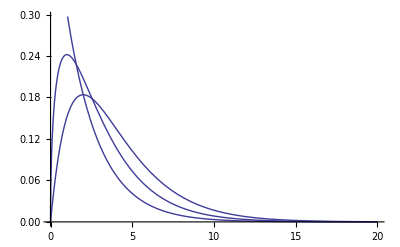

```mathematica
Plot[Table[PDF[ChiSquareDistribution[i],x],{i,2,4}],{x,0,20}]
```

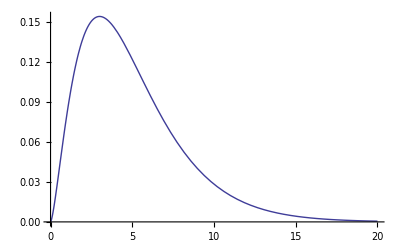

```mathematica
Plot[PDF[ChiSquareDistribution[5],x],{x,0,20}]
```

8.2-7

```mathematica
Pr(-2∑_(i=1)^n Log[Subscript[F, i](Subscript[X, i])]≤y)=Pr(∑_(i=1)^n Log[Subscript[F, i](Subscript[X, i])]≤-y/2)
```

```mathematica
Pr(Log[Subscript[F, i](Subscript[X, i])]>=-t/2)=Pr(Subscript[F, i](Subscript[X, i])>=ⅇ^(-t/2))=P(Subscript[X, i]>=Subscript[x, i])=1-Subscript[F, i](Subscript[x, i])=1-ⅇ^(-t/2)
```

```mathematica
T=-2Log[Subscript[F, i](Subscript[X, i])]
```

8.2-9

```mathematica
σ^2/n
```

8.2-10

```mathematica
3;1/3
```

8.2-11

```mathematica
(ⅇ^(-β x) x^(α-1) β^α)/Γ[α];X=Y^2;(ⅇ^(-β y^2) y^(2(α-1)) β^α)/Γ[α] 2y;
```

```mathematica
∫_0^∞ (ⅇ^(-β y^2) y^(2(α-1)) β^α)/Γ[α] 2y yⅆy=∫_0^∞ 2(ⅇ^(-β y^2) y^(2α) β^α)/Γ[α] ⅆy=2 β^α/Γ[α]∫_0^∞ ⅇ^(-β y^2) y^(2α) ⅆy=
2 β^α/Γ[α](1/2∫_0^∞ ⅇ^(-β y^2) y^(2α-1) ⅆ y^2)=2 β^α/Γ[α](1/2(-β)∫_0^∞ ⅇ^(-β y^2) y^(2α-1) ⅆ(-y^2/β))=
2 β^α/Γ[α](1/2(-1/β)∫_0^∞ y^(2α-1) ⅆ(ⅇ^(-β y^2)))=2 β^α/Γ[α](1/2(-1/β)( y^(2α-1) (ⅇ^(-β y^2))|-∫_0^∞ ⅇ^(-β y^2) ⅆ(y^(2α-1))))=
2 β^α/Γ[α](1/2(-1/β)( y^(2α-1) (ⅇ^(-β y^2))|-(2α-1)∫_0^∞ ⅇ^(-β y^2)y^(2α-2) ⅆy))
```

```mathematica
2 β^α/Γ[α](1/2(-1/β)(2α-1)( -∫_0^∞ ⅇ^(-β y^2)y^(2α-2) ⅆy));
2(1/2)^(m/2)/Γ[m/2](1/2(-2)(m-1)( -∫_0^∞ ⅇ^(-y^2/2)y^(m-2) ⅆy))=2(1/2)^(m/2)/Γ[m/2]((m-1)∫_0^∞ ⅇ^(-y^2/2)y^(m-2) ⅆy)=
2(1/2)^(m/2)/Γ[m/2]((m-1)∫_0^∞ ⅇ^(-y^2/2)y^(m-2) ⅆy)
```

```mathematica
∫_0^∞ ⅇ^(-y^2/2) ⅆy=(√(2π))/2;2(1/2)^(m/2)/Γ[m/2](m-1)(m-3)...∫_0^∞ ⅇ^(-y^2/2) ⅆy=(√(2π))/2...
```

```mathematica
∫_0^∞ ⅇ^(-y^2/2) y^1 ⅆy=1;2(1/2)^(m/2)/Γ[m/2](m-1)(m-3)...∫_0^∞ ⅇ^(-y^2/2) y^1 ⅆy=1...
```

```mathematica
∫_0^∞ ⅇ^(-y^2/2) yⅆy
```

1

```mathematica
y^2/2=x;y=(2x)^(1/2);(1/2)^(m/2)/Γ[m/2]∫_0^∞ ⅇ^(- y^2/2)2 y^m ⅆy=(1/2)^(m/2)/Γ[m/2]∫_0^∞ ⅇ^(- x)2 (2x)^(m/2) 1/2(2x)^(-1/2)2ⅆx=
(1/2)^(m/2)/Γ[m/2]∫_0^∞ ⅇ^(- x) (2x)^(m/2) (2x)^(-1/2)2ⅆx=(1/2)^(m/2)/Γ[m/2]∫_0^∞ ⅇ^(- x) (2x)^(m/2-1/2) 2ⅆx=(1/2)^(m/2)/Γ[m/2](2)^(m/2-1/2)2∫_0^∞ ⅇ^(- x) x^(m/2-1/2) ⅆx=
```

Theorem
8.3.4

```mathematica
Subscript[x, 1]^(->)=Subscript[c, 1] Subscript[y, 1]^(->)+Subscript[c, 2] Subscript[y, 2]^(->)+Subscript[c, 3] Subscript[y, 3]^(->);({{D[Subscript[x, 1]^(->), Subscript[y, 1]^(->)], D[Subscript[x, 1]^(->), Subscript[y, 2]^(->)], D[Subscript[x, 1]^(->), Subscript[y, 3]^(->)]}, {□, □, □}, {□, □, □}})=({{Subscript[c, 1], Subscript[c, 2], Subscript[c, 3]}, {□, □, □}, {□, □, □}});({{Subscript[d, 1], □, □}, {Subscript[d, 2], □, □}, {Subscript[d, 3], □, □}})
```

8.3-1

```mathematica
n OverHat[σ^2]/σ^2;(ⅇ^(-1/2 x) x^((n-1)/2-1) (1/2)^((n-1)/2))/Γ[(n-1)/2];(n OverHat[σ^2]/σ^2)^((n-1)/2-1)
```

8.3-3

```mathematica
({{1/(√3)}, {1/(√3)}, {1/(√3)}});1/(√3)x+1/(√3)y+1/(√3)z=0;({{1}, {-1}, {0}});x-y =0;({{1}, {1}, {-2}});
```

```mathematica
({{1/(√3)}, {1/(√3)}, {1/(√3)}});({{1}, {0}, {0}});({{0}, {1}, {0}});({{1}, {0}, {0}})-1/(√3)({{1/(√3)}, {1/(√3)}, {1/(√3)}})=({{2/3}, {-1/3}, {-1/3}});({{2/(√6)}, {-1/(√6)}, {-1/(√6)}});({{1/(√3)}, {1/(√3)}, {1/(√3)}});
({{0}, {1}, {0}})-1/(√3)({{1/(√3)}, {1/(√3)}, {1/(√3)}})+1/(√6)({{2/(√6)}, {-1/(√6)}, {-1/(√6)}})=({{0}, {1/3}, {-1/3}});({{0}, {1/(√2)}, {-1/(√2)}});
```

```mathematica
({{0}, {1/(√2)}, {-1/(√2)}});({{2/(√6)}, {-1/(√6)}, {-1/(√6)}});({{1/(√3)}, {1/(√3)}, {1/(√3)}});
```

8.3-5

```mathematica
({{1, 1}, {1, -1}})({{Subscript[X, 1]}, {Subscript[X, 2]}});({{1/(√2), 1/(√2)}, {1/(√2), -1/(√2)}})({{(Subscript[X, 1]-μ)/μ}, {(Subscript[X, 2]-μ)/σ}})=({{1/(√2)(Subscript[X, 1]-μ)/μ+1/(√2)(Subscript[X, 2]-μ)/σ}, {1/(√2)(Subscript[X, 1]-μ)/μ-1/(√2)(Subscript[X, 2]-μ)/σ}})
```

8.3-7

```mathematica
Pr(n OverHat[σ^2]/σ^2≤1.5n);20;
```

```mathematica
Pr(0.5<=n OverHat[σ^2]/σ^2≤1.5n)
```

```mathematica
CDF[ChiSquareDistribution[20],1.5*21]
```

0.951074

8.3-9

```mathematica
Pr(20 OverHat[σ^2]/4≥20*9.4/4)
```

```mathematica
CDF[ChiSquareDistribution[19],20*9.4/4]//N
```

0.999643

8.4-1

```mathematica
2∫_0^∞ (Γ((m+1)/2))/((m π)^(1/2)Γ(m/2))(1+x^2/m)^(-(m+1)/2)x^2 ⅆx=
```

```mathematica
y=(x^2/m)/(1+x^2/m);y=(1-y)x^2/m;y/(1-y)=x^2/m;1/(1-y)=1+x^2/m;√(m y/(1-y))=x;
```

```mathematica
D[√(m y/(1-y)),y]//Simplify
```

m/(2 (-1+y)^2 √(-(m y)/(-1+y)))

```mathematica
(1/(1-y))^(-(m+1)/2)y/(1-y)1/((1-y)^2 √(y/(1-y)));(1-y)^((m+1)/2-1-2+1/2)y^(1/2);α=3/2;β=(m-2)/2
```

```mathematica
2(Γ((m+1)/2))/((m π)^(1/2)Γ(m/2))m (√m)/2(Γ(3/2)Γ((m-2)/2))/(Γ((m+1)/2))=m/(π)^(1/2)(1/2(π)^(1/2))/((m-2)/2)=m/(m-2)
```

8.4-2

```mathematica
(n^(1/2)(X^--μ))/(Y/(n-1))^(1/2);(X^--μ)/(σ̂)>k ->(√17 4 X^--μ)/(σ̂)>√17 4k;
```

```mathematica
Solve[√17 4k==1.746,k]
```

{{k→0.105867}}

8.4-3

```mathematica
((Subscript[X, 1]+Subscript[X, 2])/(√2))/(((Subscript[X, 3]^2+Subscript[X, 4]^2+Subscript[X, 5]^2)^(1/2))/(√3))
```

8.4-5

```mathematica
1/2 σ^2;(Subscript[X, 1]+Subscript[X, 2])^2/(Subscript[X, 1]-Subscript[X, 2])^2;-2<=(Subscript[X, 1]+Subscript[X, 2])/(√((Subscript[X, 1]-Subscript[X, 2])^2))<=2;√((Subscript[X, 1]-(Subscript[X, 1]+Subscript[X, 2])/2)^2+(Subscript[X, 2]-(Subscript[X, 1]+Subscript[X, 2])/2)^2)
```

```mathematica
((Subscript[X, 1]+Subscript[X, 2])/(√2 σ))/((√((Subscript[X, 1]-Subscript[X, 2])^2))/(√2 σ))=2
```

```mathematica
CDF[StudentTDistribution[1],2]-CDF[StudentTDistribution[1],-2]//N
```

0.704833

8.4-7

```mathematica
((m-1/2)(m-1/2-1)(m-1/2-2)... 1/2 √π)/((m-1)(m-2)(m-3)...1 m^(1/2))
```

```mathematica
(1/2 3/2 5/2 7/2 9/2... √π)/(1*2*3*4*5... m^(1/2))=(1*3*5*7*9*11... √π)/(2*4*6*8*10... m^(1/2))=((2π)^(1/2)(2m-2)^(2m-2+1/2)(2m-1)/2 ⅇ^(-(2m-2))√π)/(((2π)^(1/2)(m-1)^(m-1+1/2)ⅇ^(-m-1))^2 2^(2(m-1))m^(1/2))=((2m-2)^(1/2)(2m-1)/2 √π)/((2π)^(1/2)(m-1)m^(1/2))=1
```

8.5-1

```mathematica
-c<=(Subscript[X, n]^--μ)/(σ/n^(1/2))≤c;c=Φ^-1((1+γ)/2)
```

8.5-3

```mathematica
-c<=(Subscript[X, n]^--μ)/(σ'/n^(1/2))≤c;c=(Subscript[T, n-1])^-1((1+γ)/2);(Subscript[X, n]^--(c σ')/n^(1/2),Subscript[X, n]^-+(c σ')/n^(1/2))
```

```mathematica
(2(c σ')/n^(1/2))^2=(4 c^2)/n σ'^2;(4 c^2)/n(∑_(i=1)^n (Subscript[X, i]-Subscript[X, n]^-)^2)/σ^2 σ^2/(n-1);n=5,γ=0.95;
```

```mathematica
(4(2.776)^2)/5 4 σ^2/4
```

6.16494 σ^2

8.5-5

```mathematica
χ^2,n-1;ChiSquareDistribution
```

```mathematica
Subscript[c, 1]=0;Subscript[c, 2]=chi^-1(γ)
```

8.5-8

```mathematica
(2*0.3)/(1-0.9)
```

6.

8.5-9

```mathematica
(4.7,5.3);θ-1/2<=4.7,θ+1/2≥5.2;(4.8,5.2);Z=0.6;(2*0.1)/(1-0.6)=0.5;4*0.1(1-0.1)
```

8.5-10

```mathematica
0.1 ⅇ^(-0.1θ);
```

```mathematica
∫_4.8^5.2 0.1 ⅇ^(-0.1θ)ⅆθ=ⅇ^-0.48-ⅇ^-0.52;0.1 ⅇ^(-0.1θ)/(ⅇ^-0.48-ⅇ^-0.52);
```

```mathematica
0.1 ⅇ^(-0.1θ)/(ⅇ^-0.48-ⅇ^-0.52)
```

4.12153 ⅇ^(-0.1 θ)

```mathematica
∫_4.9^5.1 4.122 ⅇ^(-0.1θ)ⅆθ
```

0.500032

```mathematica
∫_4.7^5.3 4.122 ⅇ^(-0.1θ)ⅆθ
```

1.5003

```mathematica
5c
```

```mathematica
ⅇ^-0.5
```

0.606531

8.5-11

```mathematica
∫_0^p 1/(√(x(1-x)))ⅆx=∫_0^(√p) 1/(z √(1-z^2))2zⅆz=∫_0^(√p) 2/(√(1-z^2))ⅆz=2ArcSin[√p]
```

```mathematica
z=√x;x=z^2;
```

```mathematica
D[2ArcSin[√x],x]
```

1/(√(1-x) √x)

```mathematica
Pr(|(2ArcSin[√(Subscript[X, n]^-)]-2ArcSin[√p])/(1/n)|<c)=Pr(-c<(2ArcSin[√(Subscript[X, n]^-)]-2ArcSin[√p])/(1/n)<c)
```

```mathematica
2ArcSin[√(Subscript[X, n]^-)]-1/n c<2ArcSin[√p];Sin[ArcSin[√(Subscript[X, n]^-)]-1/(2n)c]<√p<Sin[ArcSin[√(Subscript[X, n]^-)]+1/(2n)c]
Sin[ArcSin[√(Subscript[X, n]^-)]-1/(2n)c]^2<p<Sin[ArcSin[√(Subscript[X, n]^-)]+1/(2n)c]^2;
```

```mathematica
c=Φ^-1((1+γ)/2);
```

Example
8.6.3

```mathematica
√(2/3150)//N
```

0.0251976

8.6-2

```mathematica
Subscript[μ, 1]=(σ^2 Subscript[μ, 0]+n Subscript[ν, 0]^2 Subscript[x, n]^-)/(σ^2+n Subscript[ν, 0]^2)=(1/τ Subscript[μ, 0]+n 1/Subscript[λ, 0] Subscript[x, n]^-)/(1/τ+n 1/Subscript[λ, 0])
```

```mathematica
Subscript[ν, 1]^2=(1/τ 1/Subscript[λ, 0])/(1/τ+n 1/Subscript[λ, 0])
```

8.6-3

```mathematica
(τ/(2π))^(n/2)Exp[-1/2 τ∑_(i=1)^n (Subscript[x, i]-μ)^2] τ^(Subscript[α, 0]-1)Exp[-Subscript[β, 0] τ]
```

8.6-4

```mathematica
τ^((n-1)/2-1)Exp[-τ Subscript[s, n]^2/2]
```

```mathematica
v=Subscript[s, n]^2 τ;(v/Subscript[s, n]^2)^((n-1)/2-1)Exp[-v/2];m/2=(n-1)/2
```

8.6-7

```mathematica
E[μ]=Subscript[μ, 0]=0;E[τ]=Subscript[α, 0]/Subscript[β, 0]=1;Var[τ]=Subscript[α, 0]/Subscript[β, 0]^2=4;
```

```mathematica
Subscript[α, 0]=4 Subscript[α, 0]^2;Subscript[α, 0]=1/4;the mean does exist;
```

8.6-10

```mathematica
E[μ]=Subscript[μ, 0]=0;E[τ]=Subscript[α, 0]/Subscript[β, 0]=2;Var[τ]=Subscript[α, 0]/Subscript[β, 0]^2=E[τ^2]-E[τ]^2=5-4=1;Subscript[β, 0]=2,Subscript[α, 0]=4;
```

```mathematica
((Subscript[λ, 0] Subscript[α, 0])/Subscript[β, 0])^(1/2)μ;
```

```mathematica
Pr((4 Subscript[λ, 0])^(1/2)μ<(4 Subscript[λ, 0])^(1/2)1.412)=
```

8.6-15

```mathematica
Subscript[μ, 1]=(Subscript[λ, 0] Subscript[μ, 0]+n Subscript[x, n]^-)/(Subscript[λ, 0]+n);Subscript[λ, 1]=Subscript[λ, 0]+n;Subscript[α, 1]=Subscript[α, 0]+n/2;Subscript[β, 1]=Subscript[β, 0]+1/2 Subscript[s, n]^2+(n Subscript[λ, 0](Subscript[x, n]^--Subscript[μ, 0])^2)/(2(Subscript[λ, 0]+n))
```

```mathematica
Subscript[α, 1]=Subscript[α, 0]+n/2=2+11/2=15/2;2 Subscript[α, 1]=15;
```

```mathematica
Pr(<=U≤);
```

Theorem 8.7.1

```mathematica
∑_(i=1)^n (Subscript[X, i]-μ)^2=∑_(i=1)^n (Subscript[X, i]-Subscript[X, i]^-)^2+n(Subscript[X, i]^--μ)^2;
```

```mathematica
∑_(i=1)^n (Subscript[X, i]-Subscript[X, i]^-)^2=∑_(i=1)^n (Subscript[X, i]-μ)^2-n(Subscript[X, i]^--μ)^2
```

8.7-1

```mathematica
θ;θ=(∑_(i=0)^n Subscript[x, i])/n;
```

8.7-2

```mathematica
E[Subscript[X, i]^k]=E[X^k]
```

8.7-3

```mathematica
1/n∑_(i=1)^n Subscript[X, i]^2-1/(n-1)∑_(i=1)^n (Subscript[X, i]-Subscript[X, i]^-)^2
```

8.7-5

```mathematica
∑_(x=0)^∞ (δ(x)ⅇ^-λ λ^x)/(x!)=ⅇ^λ;∑_(x=0)^∞ (δ(x)λ^x)/(x!)=ⅇ^(2λ);
```

```mathematica
(δ(x)λ^x)/(x!)=(2λ)^x/(x!);δ(x)=2^x
```

8.7-7

```mathematica
δ(1,1,...,1)p^n
```

8.7-9

```mathematica
∑_(x=0)^∞ (δ(x)ⅇ^-λ λ^x)/(x!)=ⅇ^(-2λ);∑_(x=0)^∞ (δ(x)λ^x)/(x!)=ⅇ^-λ;
```

```mathematica
(δ(x)λ^x)/(x!)=(-λ)^x/(x!);δ(x)=(-1)^x
```

8.7-11

```mathematica
Var(X)=4 σ^2;Var(Y)=σ^2;θ̂=α Subscript[X, m]^-+(1-α)Subscript[Y, n]^-;
```

```mathematica
Var(θ̂)=α^2 (4 σ^2)/m+(1-α)^2 σ^2/n;2α (4 σ^2)/m+2(1-α)(-1)σ^2/n
```

```mathematica
Solve[2α (4 σ^2)/m+2(1-α)(-1)σ^2/n==0,α]
```

{{α→m/(m+4 n)}}

8.7-13

```mathematica
E[Subscript[δ, 0](T)]=E[E[δ(X)|T]]=E[δ(X)];
```

```mathematica
Var[δ(X)]=E[Var[δ(X)|T]]+Var[E[δ(X)|T]];
```

Example 8.8.2

```mathematica
(x/p-(1-x)/(1-p))^2//Expand
```

1/(1-p)^2-(2 x)/(1-p)^2-(2 x)/((1-p) p)+x^2/(1-p)^2+x^2/p^2+(2 x^2)/((1-p) p)

```mathematica
1/(1-p)^2-(2 p)/(1-p)^2-(2 p)/((1-p) p)+p/(1-p)^2+p/p^2+(2 p)/((1-p) p)//Simplify
```

1/(p-p^2)

8.8

```mathematica
(1/(2 Subscript[θ, 2]))^2 2n;
```

```mathematica
D[Exp[μ t+1/2 σ^2 t^2],{t,3}]/.t->0
```

μ^3+3 μ σ^2

8.8-1

```mathematica
D[1/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)(x-μ)^2),μ]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ))/(√(2 π) σ^3)

```mathematica
D[1/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)(x-μ)^2),{μ,2}]
```

((ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ)^2)/σ^4-(ⅇ^(-(x-μ)^2/(2 σ^2)))/σ^2)/(√(2 π) σ)

```mathematica
Integrate[ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ)^2,{x,-∞,∞},Assumptions->σ>0]
```

√(2 π) σ^3

8.8-2

```mathematica
p(1-p)^x
```

```mathematica
D[Log[p]+x Log[(1-p)],{p,2}]
```

-1/p^2-x/(1-p)^2

```mathematica
-(-1/p^2-((1-p)/p)/(1-p)^2)
```

8.8-3

```mathematica
(ⅇ^-λ λ^x)/(x!)
```

```mathematica
-λ+x Log[λ]-Log[x!]
```

```mathematica
D[-λ+x Log[λ]-Log[x!],{λ,2}]
```

-x/λ^2

```mathematica
-λ/λ^2=-1/λ
```

```mathematica
-(-1/λ)
```

8.8-4

```mathematica
D[1/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)(x-μ)^2),σ]
```

```mathematica
D[-Log[(2 π)^(1/2)σ]-1/(2 σ^2)(x-μ)^2,{σ,2}]
```

-(3 (x-μ)^2)/σ^4+1/σ^2

```mathematica
-(-(3 σ^2)/σ^4+1/σ^2)//Simplify
```

2/σ^2

8.8-5

```mathematica
D[-Log[(2 π)^(1/2)]-1/2 Log[v]-1/(2v)(x-μ)^2,{v,2}]
```

1/(2 v^2)-(x-μ)^2/v^3

```mathematica
-(1/(2 v^2)-v/v^3)//Simplify
```

1/(2 v^2)

8.8-9

```mathematica
1/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)x^2)
```

```mathematica
√(π/2)|X|
```

```mathematica
Integrate[x 1/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)x^2),{x,0,∞},Assumptions->σ>0]
```

σ/(√(2 π))

```mathematica
Integrate[(π x^2)/2 1/((2 π)^(1/2)σ)ⅇ^(-1/(2 σ^2)x^2),{x,-∞,∞},Assumptions->σ>0]
```

(π σ^2)/2

Example
9.1.5

```mathematica
Pr(Subscript[X, n]^-≤Subscript[μ, 0]-c)=Pr((Subscript[X, n]^--μ)/(σ/n^(1/2))≤(Subscript[μ, 0]-c-μ)/(σ/n^(1/2)))
```